```mathematica
f[x_] := 0.2 * PDF[NormalDistribution[1,5],x] + 0.3 * PDF[NormalDistribution[-2, 1],x] + 0.5 *PDF[ NormalDistribution[2,3],x]
g[x_] = 2.25*PDF[NormalDistribution[0, 5.1],x]
```

0.176004 ⅇ^(-0.0192234 x^2)

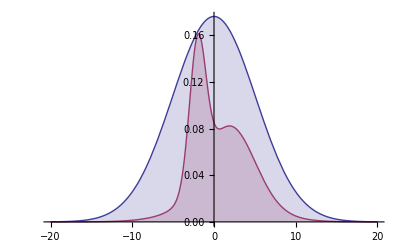

```mathematica
Plot[{g[x], f[x]},{x,-20,20},Filling->Axis]
```

```mathematica
data = {-0.7738800195010178,-0.43560743882710984,-3.411852816403015,2.9334362330968973,-3.0189022703216235,4.290669305587112,-1.4230549947143687,1.8138379236299733,-0.9622514085450415,2.624755645972602,1.76470527086134,9.247073079161725,1.5468023437632636,-1.565822506965196,2.1295651099871615,-2.046676391474828,9.59398256992576,1.9887304663115675,1.1649554465317458,-2.601343175690097,2.7103366958192647,9.098688360979558,2.4607825672144132,9.977121500914917,-0.6595236404353995,1.9879302559651273,5.717375791955247,-0.592985769994494,7.133731047041692,1.5708507812261685,-2.21247017346163,-1.3972582046200652,-0.41854567417762434,-3.37366797975152,-3.788894908906337,-0.8726701292676544,-2.1539711256541736,5.2699111421406695,0.5490370013876968,-1.3079526304437161,1.7322859155982742,8.245955298477131,-2.583842228384943,-0.46759089685103694,4.59293726778019,2.063423298548275,-1.56786943489608,-0.5802959182921543,-1.1570929743318974,-0.6603851433505974,1.019791282228284,-0.8801682507401458,5.165777849222476,4.522077419382851,-2.0791266486357998,-2.875927655966291,-2.4460246039400566,-3.1502919297723606,-2.357536075605078,-0.8579117598521198,-2.457027362210143,1.231506283341158,3.7935481399581636,-3.556535656422863,3.386693926725214,-0.35269087123270726,0.3285141674513419,4.609431412187655,-1.3395021686236546,7.4043583596848,-2.3297623221932042,1.146073438856281,2.4748905033014736,-1.7663339993267655,-1.3144755317019698,-1.4789515344650077,-1.8778780268015325,-0.8710447776379937,-0.21994825278681507,-2.658992885148427,-3.672845896097465,-1.8238075917078436,1.1272589026350228,-1.9411492983099232,-0.41045284714649544,-2.4804719479068207,1.776657969138408,-2.552309266262354,2.854602099320404,11.689431169777224,3.083435890772149,-1.574770734022329,-0.9447771783499621,-2.725251059507519,0.4406855303457904,-2.7716095128220735,-0.2675313278084448,1.7200598349557945,6.855375617235523,0.8984444018216651,-1.4002477113207221,-1.0974114104822768,-2.573305174290362,-1.8804668210354487,0.6207935184366049,-0.3688350402479401,-2.922066526484323,-1.8881413663305058,12.971782539682653,-5.166469364267249,1.7366348369084252,4.510917644653809,4.781459438477233,-2.107549808040272,-2.6277686002603966,8.135893366856504,4.212472318659858,-1.5542790140584213,-0.28044200646576467,-0.36997628639453906,5.6020968444648735,-0.41287113017412835,-1.2121461447240067,-1.7270981513675896,-1.3539731990482555,4.891386708085566,-0.21339178617496035,6.56792898338858,-3.9723294372985682,5.695841147830449,1.6927446287339603,-1.907773571325535,3.194393941932992,0.4247537855639094,-1.7834030966345935,7.157365733224358,2.392512075895116,4.099197512814364,-4.799996654716151,2.003278930332157,-2.4217270805707756,-1.5687667511237313,-2.1906464129014576,-0.9664776674612043,-2.9900948466241233,2.3024961002635553,1.6003372285181214,-1.6955033716759393,-3.06887166744684,1.1477061759354807,-1.3546922081735773,0.2361597347647284,6.890324786212281,2.1161387715790734,-1.9859676311863135,-0.948586801642934,-1.9957569446486747,5.587322200349755,2.4136133778211986,-2.995692898373923,-2.737921259799897,-2.4120892161317236,0.018298579742646925,4.390890512264605,3.314734150732571,0.9114762675552281,6.050196479876904,5.548889274157461,-2.1028575404478476,-2.1185860484551107,-2.2467734912706967,-0.7689212962432053,-3.13868665901896,1.80653614647253,-2.8791711468602115,3.137625619779257,-1.802098241025522,2.2171958104960092,-1.383520290155519,-3.857020692501547,-1.9527092317372128,0.10516099034068294,5.7563461422619095,-2.5697796442709353,4.337162379059999,-0.420032846756659,5.013647327585388,-4.5092320548774545,-6.634862559956464,1.9613111086938178,3.2113861071654286,0.8992624762411228,0.2709372569900623,-3.061763013501232,0.9197778960003397,1.1343683342101587,-1.1217886732929343,-2.2250894559988055,-0.9720480444675044,-1.7315064879027635,-1.939617403886477,3.2092212236219706,-0.6319383470603603,3.9097521301362543,-2.706071280585731,0.9001884184605855,-2.7575671676275935,12.158029490301244,-2.861952467715637,-2.1694121643765385,7.412133485101861,-1.0608534363841762,-7.206415601186038,3.8601664994846883,-3.44245469254479,6.7527211759354735,-1.554543070381019,1.7713942576051525,2.235254811268498,0.39751190549109494,4.944887100825634,1.236022013420842,-1.4108541142688917,-0.6988127169796181,4.848422925406238,-0.1332371033463624,-0.7131611123067585,-1.1540156950846021,-1.886163107901777,2.671873596543758,-0.2238328224179531,-0.4598218484588892,0.0628145682270338,4.994189268248073,6.677494127155222,2.6800986589775637,2.1489380564282454,1.6547199173979323,-5.078367421793548,1.7047214374387099,5.623472199663075,-2.6599981992920334,-0.29421870346102486,9.754485020642358,1.8268942529358154,6.077764653591978,2.2934173702378247,-1.963442517836782,1.3094980281245587,-3.0745643832998635,4.667013679309585,7.146366813584728,2.6398169787782684,3.175729947786728,-1.4027925934057701,7.7255309216463175,4.442910634909786,10.022582790265862,2.7328888967654823,-1.0740033144836554,-4.329225085351181,7.2555673716547915,2.1755741254305945,-1.6526600265259237,1.542947070622902,-1.521318016494984,-1.371868607155458,4.018160983976634,2.6201414928653746,-4.789418500180409,-1.1105100600743314,5.861840913209477,-1.475159211669531,2.4465275966723135,3.5352329867052865,2.98160250348941,-3.289133074737194,0.4099629753692269,4.667624473473449,5.128430660718401,3.90012278502164,1.6012345373978998,-1.281453905147124,4.272016256701834,-2.1310752456760977,-0.7973625178932771,-6.769088291151006,-2.4956351367147276,-2.673254453825993,-2.669735299503328,-1.149278912321098,-2.091205700155487,1.1929369925144089,1.3745456247522103,-0.5036076570977037,5.498038935455585,1.020543433581107,1.2270089061065994,5.092689133212819,-6.342263179639684,-6.1538521447833014,-0.7519457890130945,-5.182461331589057,0.44185854745800945,5.637971450939491,0.5991077684379793,5.142756654157265,-3.4901251354447824,-0.31976824182382946,2.5673033259489264,1.274794006205722,4.770927242103047,2.316953202988927,2.8180352713575005,3.6972159356092087,-0.4157955089038421,6.875243130633426,4.939368163312224,-1.764651738154834,-1.4238384403463786,1.0050575784972695,-3.2191904215110414,-4.169677161216928,2.6125873805038173,-3.117448161784319,-1.7163135585892717,-3.329758000973304,-1.9632775459429161,1.7061665371177135,0.7289434874203318,1.253933123788991,-0.010371440872154913,8.485365596087236,-2.0185490472207164,-2.503865329771089,-2.057919659604749,1.4649062875717958,0.931849463624756,-3.3813322074080805,-1.0692127795315214,0.9614739687269895,3.005954595572889,-3.90277495046578,6.49383292745612,6.620225653608813,1.1840211771284959,-0.7397379913776414,1.3756582419177525,3.4610336540020477,-1.3806124143343261,-0.5430459542039401,-2.0490891590581253,-3.036748546998523,4.552872083464998,2.4401519241510887,-2.2972451082503182,-2.107500125565652,-1.8624415827970509,0.16006744881814594,-2.327628096496249,-1.5333258758291206,5.571490935077645,1.5817366639986696,-1.9512935911848406,-5.693685788490061,-2.702404371830642,1.351356825089517,6.55520245370986,0.8019625484835169,-4.142070624673506,-2.094262974709284,-2.020808163691331,-2.900414412860841,-4.760414854149371,2.057457860122973,4.723361754294066,2.4466164627767273,-3.111925757174922,-1.4465845076560164,-0.8690164264321978,4.558637224028136,-2.505252461324342,3.7576000694565166,-1.247293688397225,3.3387063919372846,-2.253950946571652,-6.585757953966439,-0.9778314200680389,-2.234672831038466,1.5041002851777723,1.4512776430915864,4.28194822276348,6.954290496350122,-4.535765804420028,-1.5230078264222955,-1.1833497630862162,-1.7541754906982512,-1.9616901672949454,-4.751553606158639,-1.41672546333573,-1.6543691904288844,6.430806509551651,-3.3733900144570494,-1.7247635580243927,4.91147441410002,-1.6343223698897518,1.4227160158086751,-1.8231593805286856,-3.8810226628061972,-1.0817839176921495,-0.39589444203208135,-2.291971251926457,-1.8283209879395057,3.2718034842310346,4.8801458692169755,-1.3871916379378213,0.31532479418556114,-0.1987707356788908,4.11804853573374,-2.2764752346221617,-4.201186179486273,-1.389826715620456,-0.9998019586934319,-3.343185258832613,-3.0184633805894645,-0.030742449861881127,-3.9872571466860904,1.2207329091449042,-0.4105813003429617,-2.293817665770347,2.7372020886981008,-0.9859966241989264,5.827614410677261,2.492502824430042,-2.4909907853806,-1.4676914658279756,6.537909084614272,-1.9660265455857564,-1.8895218444082174,-1.8514318998224568,-1.0822292229593398,-3.381567565025751,-1.1645754404351423,-2.332204942468048,1.5944587267856094,-0.18275382902246262,1.2658361787763421,-5.137173060316206,3.1534655226123443,4.514998529652009,-0.2564686399905949,0.8342436160431479,-2.5296470135896283,6.506194063215641,1.7811428249310126,2.9015348842057085,2.160278134396432,1.6375035484050846,4.82201232853669,-3.595849924875232,2.085865690915805,-1.020227115708344,-9.404607529268098,-2.9874667954174847,-1.5567266791396366,1.1071296793253476,3.098137978030198,2.6448210670430847,-0.8246879826243156,8.3705955588232,1.4226269447238822,-2.5249373358476888,3.0907322318928783,4.307018684541303,-2.5373178851988802,-1.360301768084954,-1.7608800366316617,-4.5382685839496055,2.732703463456759,-0.3507019881747131,-1.544544309180992,3.1488967256410065,-1.8322516568096194,5.031681183209761,-3.1594954051084185,2.708055127864251,2.823884021793554,-2.859632022232684,-0.800682170492766,-2.0308485724813146,0.6341450197914362,-2.5361868493599427,-1.9841271563608407,-0.8767397179120482,5.930831917478919,-3.9097520553834313,1.1589867048036484,-0.30927059989297145,5.32702745425763,4.478465236562602}
```

{-0.77388,-0.435607,-3.41185,2.93344,-3.0189,4.29067,-1.42305,1.81384,-0.962251,2.62476,1.76471,9.24707,1.5468,-1.56582,2.12957,-2.04668,9.59398,1.98873,1.16496,-2.60134,2.71034,9.09869,2.46078,9.97712,-0.659524,1.98793,5.71738,-0.592986,7.13373,1.57085,-2.21247,-1.39726,-0.418546,-3.37367,-3.78889,-0.87267,-2.15397,5.26991,0.549037,-1.30795,1.73229,8.24596,-2.58384,-0.467591,4.59294,2.06342,-1.56787,-0.580296,-1.15709,-0.660385,1.01979,-0.880168,5.16578,4.52208,-2.07913,-2.87593,-2.44602,-3.15029,-2.35754,-0.857912,-2.45703,1.23151,3.79355,-3.55654,3.38669,-0.352691,0.328514,4.60943,-1.3395,7.40436,-2.32976,1.14607,2.47489,-1.76633,-1.31448,-1.47895,-1.87788,-0.871045,-0.219948,-2.65899,-3.67285,-1.82381,1.12726,-1.94115,-0.410453,-2.48047,1.77666,-2.55231,2.8546,11.6894,3.08344,-1.57477,-0.944777,-2.72525,0.440686,-2.77161,-0.267531,1.72006,6.85538,0.898444,-1.40025,-1.09741,-2.57331,-1.88047,0.620794,-0.368835,-2.92207,-1.88814,12.9718,-5.16647,1.73663,4.51092,4.78146,-2.10755,-2.62777,8.13589,4.21247,-1.55428,-0.280442,-0.369976,5.6021,-0.412871,-1.21215,-1.7271,-1.35397,4.89139,-0.213392,6.56793,-3.97233,5.69584,1.69274,-1.90777,3.19439,0.424754,-1.7834,7.15737,2.39251,4.0992,-4.8,2.00328,-2.42173,-1.56877,-2.19065,-0.966478,-2.99009,2.3025,1.60034,-1.6955,-3.06887,1.14771,-1.35469,0.23616,6.89032,2.11614,-1.98597,-0.948587,-1.99576,5.58732,2.41361,-2.99569,-2.73792,-2.41209,0.0182986,4.39089,3.31473,0.911476,6.0502,5.54889,-2.10286,-2.11859,-2.24677,-0.768921,-3.13869,1.80654,-2.87917,3.13763,-1.8021,2.2172,-1.38352,-3.85702,-1.95271,0.105161,5.75635,-2.56978,4.33716,-0.420033,5.01365,-4.50923,-6.63486,1.96131,3.21139,0.899262,0.270937,-3.06176,0.919778,1.13437,-1.12179,-2.22509,-0.972048,-1.73151,-1.93962,3.20922,-0.631938,3.90975,-2.70607,0.900188,-2.75757,12.158,-2.86195,-2.16941,7.41213,-1.06085,-7.20642,3.86017,-3.44245,6.75272,-1.55454,1.77139,2.23525,0.397512,4.94489,1.23602,-1.41085,-0.698813,4.84842,-0.133237,-0.713161,-1.15402,-1.88616,2.67187,-0.223833,-0.459822,0.0628146,4.99419,6.67749,2.6801,2.14894,1.65472,-5.07837,1.70472,5.62347,-2.66,-0.294219,9.75449,1.82689,6.07776,2.29342,-1.96344,1.3095,-3.07456,4.66701,7.14637,2.63982,3.17573,-1.40279,7.72553,4.44291,10.0226,2.73289,-1.074,-4.32923,7.25557,2.17557,-1.65266,1.54295,-1.52132,-1.37187,4.01816,2.62014,-4.78942,-1.11051,5.86184,-1.47516,2.44653,3.53523,2.9816,-3.28913,0.409963,4.66762,5.12843,3.90012,1.60123,-1.28145,4.27202,-2.13108,-0.797363,-6.76909,-2.49564,-2.67325,-2.66974,-1.14928,-2.09121,1.19294,1.37455,-0.503608,5.49804,1.02054,1.22701,5.09269,-6.34226,-6.15385,-0.751946,-5.18246,0.441859,5.63797,0.599108,5.14276,-3.49013,-0.319768,2.5673,1.27479,4.77093,2.31695,2.81804,3.69722,-0.415796,6.87524,4.93937,-1.76465,-1.42384,1.00506,-3.21919,-4.16968,2.61259,-3.11745,-1.71631,-3.32976,-1.96328,1.70617,0.728943,1.25393,-0.0103714,8.48537,-2.01855,-2.50387,-2.05792,1.46491,0.931849,-3.38133,-1.06921,0.961474,3.00595,-3.90277,6.49383,6.62023,1.18402,-0.739738,1.37566,3.46103,-1.38061,-0.543046,-2.04909,-3.03675,4.55287,2.44015,-2.29725,-2.1075,-1.86244,0.160067,-2.32763,-1.53333,5.57149,1.58174,-1.95129,-5.69369,-2.7024,1.35136,6.5552,0.801963,-4.14207,-2.09426,-2.02081,-2.90041,-4.76041,2.05746,4.72336,2.44662,-3.11193,-1.44658,-0.869016,4.55864,-2.50525,3.7576,-1.24729,3.33871,-2.25395,-6.58576,-0.977831,-2.23467,1.5041,1.45128,4.28195,6.95429,-4.53577,-1.52301,-1.18335,-1.75418,-1.96169,-4.75155,-1.41673,-1.65437,6.43081,-3.37339,-1.72476,4.91147,-1.63432,1.42272,-1.82316,-3.88102,-1.08178,-0.395894,-2.29197,-1.82832,3.2718,4.88015,-1.38719,0.315325,-0.198771,4.11805,-2.27648,-4.20119,-1.38983,-0.999802,-3.34319,-3.01846,-0.0307424,-3.98726,1.22073,-0.410581,-2.29382,2.7372,-0.985997,5.82761,2.4925,-2.49099,-1.46769,6.53791,-1.96603,-1.88952,-1.85143,-1.08223,-3.38157,-1.16458,-2.3322,1.59446,-0.182754,1.26584,-5.13717,3.15347,4.515,-0.256469,0.834244,-2.52965,6.50619,1.78114,2.90153,2.16028,1.6375,4.82201,-3.59585,2.08587,-1.02023,-9.40461,-2.98747,-1.55673,1.10713,3.09814,2.64482,-0.824688,8.3706,1.42263,-2.52494,3.09073,4.30702,-2.53732,-1.3603,-1.76088,-4.53827,2.7327,-0.350702,-1.54454,3.1489,-1.83225,5.03168,-3.1595,2.70806,2.82388,-2.85963,-0.800682,-2.03085,0.634145,-2.53619,-1.98413,-0.87674,5.93083,-3.90975,1.15899,-0.309271,5.32703,4.47847}

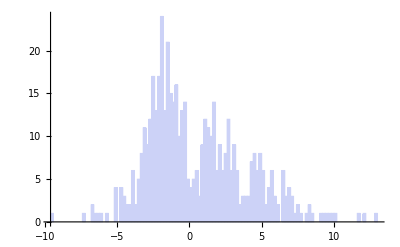

```mathematica
Histogram[data, 100]
```

```mathematica
data1 = {-2.5917637885235822,-2.5400540552101116,-0.18643298137337366,0.49594318115484415,5.278818894726803,1.4295788900908901,-1.9195773647357686,4.738837300416812,-2.7112264851078556,-0.8934532765124945,0.1121697885227453,1.6720904645513255,5.7828453413031085,-6.14896799815768,-2.1423601294112284,4.697024383667657,-3.2294628528889042,2.888775792355723,0.11797318981818859,6.699668367668305,-0.888480602042249,-2.5987130440273294,-1.8712062828285911,-1.348827200249761,1.330427095933465,0.7201053760627427,-0.7258476623775606,6.152129553730462,-2.9695674830605854,3.5601008997526886,-1.4825395076618828,-1.596366647788678,7.834819136306889,-2.3192255534325077,0.9661648199306581,0.23990017251023796,-1.0484159319811204,4.238292012727682,-3.942632322593581,-12.76011247849871,-2.1305109263337494,6.9337198836922544,-2.0837464637831213,-1.6212821285580166,4.236098990044358,-1.703367939256764,-3.232095725897696,1.772448674258938,-3.198394312431061,0.4132100614727403,-1.2478836296464646,-1.747160075699927,0.5708389690549777,-3.370793126847949,3.31892422448186,-1.37130201102401,-8.076122991506558,2.5570481760807504,-1.0346697407960281,-0.16693997094271526,0.010405137800328172,-1.5019673948384813,2.6291795186261204,0.5549081493738629,5.6886176887563025,-1.7812375705540253,3.619873602877951,-1.086894643023277,-1.1010687215164363,8.620786940060107,8.68812610122878,3.18624469840429,-0.7111983874661637,-0.7659088048426679,-6.357709336823798,-1.7489505548047066,0.9824478027580337,-0.23662186139849897,0.8484683195685321,-0.89780688010438,0.2549492757136817,-3.5260649894713763,-1.0344229636294715,-1.2841474894667142,-1.2471648288209445,-1.2056697365062796,-0.7817960428430696,6.800971888609702,-4.755839439463057,-2.3758936227215712,-1.542408326789165,3.34095076285943,3.423939273068623,1.272278742489731,-3.0351776160631614,-0.5203528533234377,-2.4902282590654705,5.931850972313343,4.677822225021187,0.9936694768889627,6.677501806187466,-0.9826796993448714,-1.75912531345109,8.12645850325244,-2.5783441749494482,6.29421012742069,-4.274165297394724,-2.8880578578313645,0.5515988496303638,-1.096826468890984,-0.5076701114093087,7.2798729768845645,-1.1814211256863543,1.8777918258201873,-2.2755252055095174,-1.402501953549914,2.9624847987000713,7.350137076210697,3.177514227798148,7.336912933291009,1.2038599868742799,3.561144381801646,-0.3220730593624331,3.5166879673550153,5.52517468375603,1.822881465481996,0.7188765964390446,-0.923061813169235,-1.6083063486308344,1.1004387825054225,-1.1960975000128253,-1.8977310919431827,-0.9008590197212892,-1.0179321563341392,8.245350974199045,-2.100714197789736,4.566552708498553,-1.3796867249044298,4.9178919045518565,11.464970092512496,-4.465236145003492,2.7913968316956757,-0.30899050251818005,-1.1870525547329882,-3.6905391980374596,-1.000496281708922,3.3116756723263867,-1.8288966889795448,8.886474353273421,-2.3793897095460808,5.216295218958805,-3.796025575532971,-7.393966984740661,5.269547539300651,3.69458511390308,3.6328804210860497,-3.2355124068017025,4.575446221257788,-1.4084383914954777,-2.841990259847501,0.6307088923305965,5.028523732295041,4.424250401731726,6.819425299783795,0.16167471527305496,-2.009465887014307,-0.6008074397459657,6.614867450682241,2.878423446342335,2.897284283740429,-1.3463620562313743,1.4333342736754733,6.290125207975683,-3.087053051603982,-0.6842437024846884,0.9997619899293764,0.5007613296843461,-3.0892995648794592,-3.415999359093089,-2.261239844485728,2.2158633565360555,-1.2405007652134017,-0.42217923020531056,5.969855017040016,3.7373020399880303,3.6625604807180925,-2.1862216908828658,0.6697038375753099,-2.172252628336174,5.766567756636723,3.0411757305327365,-1.734855631509641,-1.5396790563464078,-2.1602325057261735,-2.1497901716540766,-0.3231476435139303,2.845597627409703,-10.4758667816466,0.27520196893368104,-2.2620783284951265,2.9010773086543247,3.089311745719497,4.233322675985459,-0.10232119962901493,-4.1590555506008835,-3.9088397667345602,-0.03585406607359958,-0.9951669194019843,-1.4903908362246143,-3.514668521088002,-3.324974889844683,-3.3515903822835122,-1.797819946658801,-0.43795887396886934,-5.029416523304298,-2.0207586795143,-0.8711303277160117,4.38203055569875,3.16897119028616,1.708478286107394,-1.3945556778032429,-2.0087606431967173,1.6541706026002272,-2.3741773191667868,-3.274783663852519,4.9380722933108165,-1.2586396119340046,2.993033944764966,-3.6665412012332648,2.9990566057934447,-6.175676358445293,-2.077257302098428,0.9378697394252188,-2.2708585885295625,2.4504678111952107,3.8252308184863497,5.699590486943707,-0.9445519005348259,-2.234314011008197,-1.1807790750633373,-1.027616881913785,5.767964438752628,2.870512894231349,-1.779517461501074,-3.0224647561721993,0.9756401153188152,-1.6836891620712893,0.44624064997906776,-0.1985995699726453,0.17853997958065404,2.6605712594910504,-1.421460034508949,2.1699715918294773,5.038896464276784,0.8973638835738489,-0.8148229500649734,-1.76408403080236,-1.3180763711250814,-6.712451286899337,5.5324174764172165,-2.0320896375566706,-1.3856327030874265,-2.1172203989276066,3.104134297887812,-1.6207172624831723,5.911809835706717,1.0837129945659423,2.4680908009815012,2.3805510774191703,-2.1326263494833935,-2.258108968300105,2.3653827137997427,1.1003369635179565,5.88247145352798,7.697399267445327,-4.427061809979093,-3.2846795179594195,-3.247738383566714,7.689166501146856,3.522248866026812,2.1700136818003033,-1.1478733358583706,-1.25456960581182,-1.5526635833243794,-2.934850549272111,-1.8708336467662254,-5.051473044854006,-2.111359080005225,7.199425392756742,1.9109718421950876,-2.33584971159072,-1.5164866606703091,-1.2157340047870717,-2.6436237269993845,-7.240194228379866,-0.03320896101184657,-3.3548335829215796,1.5531724082284515,7.709144765138933,-2.0173923234711495,-1.2644296089020297,-1.911328950909062,0.3528733133225322,9.24677091140231,-3.951608383790733,-1.6562269372392466,-0.6653269970631791,1.8145518425564826,-2.356495071585579,-3.0647650518329974,-1.920894833680139,9.275167793828523,-4.488090437877269,0.27645179756678,2.147659573684088,10.719371141066139,3.2959220867351395,-1.1514071049122931,-1.88895932488331,-4.4317346818738415,2.606834855927867,1.8169150514794874,3.2178519410653026,1.2246833654275728,0.35477446326840195,-3.076982644534792,0.6323693528765341,0.039950195132422345,1.603619021093947,-1.4447210704992017,6.0212613530196215,-2.6512231985709502,2.6396299186177763,-2.374146395537153,3.1111537831093976,1.1658599773995941,-0.41740432247994197,-0.5914654230164105,0.08981537663894491,1.3171037729857322,7.032660211430593,-1.982356265747669,4.403113799918519,0.5805338845975939,-2.2464787320159103,-7.632661634800711,-1.920006180680863,-2.4563448246840376,-6.484802402080582,4.75605811306553,-0.705285618638965,3.29281045957236,1.4722920621833073,0.8036330440064232,4.201408967055191,-1.6690750444205087,-2.044856741885626,3.5572262441059004,4.167665231456699,-0.22400210950126995,3.084340165926004,1.0574945403627984,-1.4424903024313305,-1.8652367908189447,-0.7278320672748112,3.7924238472955385,-1.4603146782720628,4.982107695210827,0.19134233874498977,5.944638978161514,-0.6293649995607485,-0.2911392025978744,-1.613292191738972,5.1338775522412545,-0.28068950461449893,0.7026805764504773,-2.693141940834172,-3.443249409337997,-1.5420971449543501,3.8870447990198316,-0.8686034670218535,-1.6218616287948158,-2.5714593726926864,4.413089119067076,1.6651572469441618,-1.1654845947689458,1.6746296035648047,-1.8235195673235807,-1.9512687825276531,-1.1597692765217467,-3.2993871357209197,-3.2192465840327644,5.660399516373787,5.375326051840978,0.4333037064056362,5.361591174684472,5.698945717016828,-6.859990444291017,-3.9646802001506014,6.2217837940007605,1.8228682323853098,1.0647167230240209,-3.9599364776731103,3.4770113359941597,-2.0533384715098246,3.488960699985985,3.0831932521420313,1.9862400062136174,5.393382789884552,2.5795458987995796,-2.009778792517216,3.4076939251073934,-2.17260471320504,-3.1784111704522306,3.6392787312240733,-0.7854315211234686,0.5009671121794543,-3.6314640029853122,-0.615492452889417,3.1213562865085933,-2.9150825155696625,2.1032504628749864,5.406828880586622,4.345350243442668,3.958226766632304,-2.5658217690175964,-0.23061833412332403,3.7096257268425235,-2.3572952159257192,5.565565320264649,-0.38016122057379187,-2.104173322194825,1.0496075433971592,2.6611170786882066,-2.732828741310257,-0.3018178065599923,-1.248270067960997,-2.3288828353033897,-1.5007327885716126,-4.279183038703374,4.713199285509226,1.8891337829583363,-3.7702665855027138,-2.9750697182849817,2.690868352466816,7.278777746816595,-2.134338701007848,-1.8089877414408309,0.2989456259840191,0.81380324577228,-1.4916907845500404,1.8746928017648108,0.19903449465339848,2.5367224641859374,1.442988633614114,2.7364175323438755,-3.137349097123013,4.514135786165103,3.8317093717679915,6.376272053336139,3.572768878403933,1.3907263578108868,5.938996614347296,-2.030679209034201,-1.151470166109228,5.586514847981163,-6.7700082606911325,4.35683940719071,-1.6593035881384723,-0.18270691573206305,2.814083288270089,-2.4077414360855522,-1.4974728411610203,0.2312286160558089,5.24459355250438,-2.736280388779577,-2.6120892236086486,-2.117127196660456,3.864795557443219,0.63763274558598,7.401611587294466,-2.9344161408229215,1.2113102425988007,2.213829351925968,0.6295222090638407,-1.849236683529797,3.3605335951019755,-5.189791190945385,-4.380674733527375,7.118124419729144,1.8738870964939351,4.3664014426428945,-4.255141702319521,0.41613844618973495,-9.019528216681715,0.747923606354074,1.761313094881857,0.7719759007454299,5.626882998839974,9.682337579486168}
```

{-2.59176,-2.54005,-0.186433,0.495943,5.27882,1.42958,-1.91958,4.73884,-2.71123,-0.893453,0.11217,1.67209,5.78285,-6.14897,-2.14236,4.69702,-3.22946,2.88878,0.117973,6.69967,-0.888481,-2.59871,-1.87121,-1.34883,1.33043,0.720105,-0.725848,6.15213,-2.96957,3.5601,-1.48254,-1.59637,7.83482,-2.31923,0.966165,0.2399,-1.04842,4.23829,-3.94263,-12.7601,-2.13051,6.93372,-2.08375,-1.62128,4.2361,-1.70337,-3.2321,1.77245,-3.19839,0.41321,-1.24788,-1.74716,0.570839,-3.37079,3.31892,-1.3713,-8.07612,2.55705,-1.03467,-0.16694,0.0104051,-1.50197,2.62918,0.554908,5.68862,-1.78124,3.61987,-1.08689,-1.10107,8.62079,8.68813,3.18624,-0.711198,-0.765909,-6.35771,-1.74895,0.982448,-0.236622,0.848468,-0.897807,0.254949,-3.52606,-1.03442,-1.28415,-1.24716,-1.20567,-0.781796,6.80097,-4.75584,-2.37589,-1.54241,3.34095,3.42394,1.27228,-3.03518,-0.520353,-2.49023,5.93185,4.67782,0.993669,6.6775,-0.98268,-1.75913,8.12646,-2.57834,6.29421,-4.27417,-2.88806,0.551599,-1.09683,-0.50767,7.27987,-1.18142,1.87779,-2.27553,-1.4025,2.96248,7.35014,3.17751,7.33691,1.20386,3.56114,-0.322073,3.51669,5.52517,1.82288,0.718877,-0.923062,-1.60831,1.10044,-1.1961,-1.89773,-0.900859,-1.01793,8.24535,-2.10071,4.56655,-1.37969,4.91789,11.465,-4.46524,2.7914,-0.308991,-1.18705,-3.69054,-1.0005,3.31168,-1.8289,8.88647,-2.37939,5.2163,-3.79603,-7.39397,5.26955,3.69459,3.63288,-3.23551,4.57545,-1.40844,-2.84199,0.630709,5.02852,4.42425,6.81943,0.161675,-2.00947,-0.600807,6.61487,2.87842,2.89728,-1.34636,1.43333,6.29013,-3.08705,-0.684244,0.999762,0.500761,-3.0893,-3.416,-2.26124,2.21586,-1.2405,-0.422179,5.96986,3.7373,3.66256,-2.18622,0.669704,-2.17225,5.76657,3.04118,-1.73486,-1.53968,-2.16023,-2.14979,-0.323148,2.8456,-10.4759,0.275202,-2.26208,2.90108,3.08931,4.23332,-0.102321,-4.15906,-3.90884,-0.0358541,-0.995167,-1.49039,-3.51467,-3.32497,-3.35159,-1.79782,-0.437959,-5.02942,-2.02076,-0.87113,4.38203,3.16897,1.70848,-1.39456,-2.00876,1.65417,-2.37418,-3.27478,4.93807,-1.25864,2.99303,-3.66654,2.99906,-6.17568,-2.07726,0.93787,-2.27086,2.45047,3.82523,5.69959,-0.944552,-2.23431,-1.18078,-1.02762,5.76796,2.87051,-1.77952,-3.02246,0.97564,-1.68369,0.446241,-0.1986,0.17854,2.66057,-1.42146,2.16997,5.0389,0.897364,-0.814823,-1.76408,-1.31808,-6.71245,5.53242,-2.03209,-1.38563,-2.11722,3.10413,-1.62072,5.91181,1.08371,2.46809,2.38055,-2.13263,-2.25811,2.36538,1.10034,5.88247,7.6974,-4.42706,-3.28468,-3.24774,7.68917,3.52225,2.17001,-1.14787,-1.25457,-1.55266,-2.93485,-1.87083,-5.05147,-2.11136,7.19943,1.91097,-2.33585,-1.51649,-1.21573,-2.64362,-7.24019,-0.033209,-3.35483,1.55317,7.70914,-2.01739,-1.26443,-1.91133,0.352873,9.24677,-3.95161,-1.65623,-0.665327,1.81455,-2.3565,-3.06477,-1.92089,9.27517,-4.48809,0.276452,2.14766,10.7194,3.29592,-1.15141,-1.88896,-4.43173,2.60683,1.81692,3.21785,1.22468,0.354774,-3.07698,0.632369,0.0399502,1.60362,-1.44472,6.02126,-2.65122,2.63963,-2.37415,3.11115,1.16586,-0.417404,-0.591465,0.0898154,1.3171,7.03266,-1.98236,4.40311,0.580534,-2.24648,-7.63266,-1.92001,-2.45634,-6.4848,4.75606,-0.705286,3.29281,1.47229,0.803633,4.20141,-1.66908,-2.04486,3.55723,4.16767,-0.224002,3.08434,1.05749,-1.44249,-1.86524,-0.727832,3.79242,-1.46031,4.98211,0.191342,5.94464,-0.629365,-0.291139,-1.61329,5.13388,-0.28069,0.702681,-2.69314,-3.44325,-1.5421,3.88704,-0.868603,-1.62186,-2.57146,4.41309,1.66516,-1.16548,1.67463,-1.82352,-1.95127,-1.15977,-3.29939,-3.21925,5.6604,5.37533,0.433304,5.36159,5.69895,-6.85999,-3.96468,6.22178,1.82287,1.06472,-3.95994,3.47701,-2.05334,3.48896,3.08319,1.98624,5.39338,2.57955,-2.00978,3.40769,-2.1726,-3.17841,3.63928,-0.785432,0.500967,-3.63146,-0.615492,3.12136,-2.91508,2.10325,5.40683,4.34535,3.95823,-2.56582,-0.230618,3.70963,-2.3573,5.56557,-0.380161,-2.10417,1.04961,2.66112,-2.73283,-0.301818,-1.24827,-2.32888,-1.50073,-4.27918,4.7132,1.88913,-3.77027,-2.97507,2.69087,7.27878,-2.13434,-1.80899,0.298946,0.813803,-1.49169,1.87469,0.199034,2.53672,1.44299,2.73642,-3.13735,4.51414,3.83171,6.37627,3.57277,1.39073,5.939,-2.03068,-1.15147,5.58651,-6.77001,4.35684,-1.6593,-0.182707,2.81408,-2.40774,-1.49747,0.231229,5.24459,-2.73628,-2.61209,-2.11713,3.8648,0.637633,7.40161,-2.93442,1.21131,2.21383,0.629522,-1.84924,3.36053,-5.18979,-4.38067,7.11812,1.87389,4.3664,-4.25514,0.416138,-9.01953,0.747924,1.76131,0.771976,5.62688,9.68234}

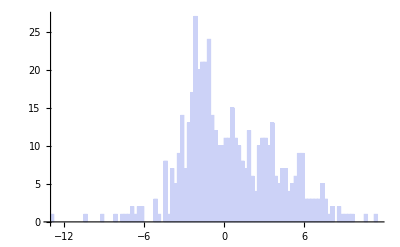

```mathematica
Histogram[data1, 100]
```

```mathematica
data2 = {0.7045249337469734,0.6910738906870368,0.47927491784001297,0.6067756833473235,0.8258573834852868,0.501210226678037,0.4940978007876636,0.3829510022892247,0.2497677853072163,0.5162618862819216,0.4243584897890095,0.1797078218947422,0.00986629544621459,0.0790973808368522,-0.3125567480640316,-0.31321386307277904,-0.04434514906906789,0.37496850969394496,0.41028785670662776,0.39506716146505155,0.04597573521645337,0.15030867984489502,0.4700184082177983,0.46576579097712645,1.0632106792479554,0.8514631318565723,1.075750940926306,0.7248783815260222,1.1095954510273407,1.5609738955996708,1.5193632416447416,1.2134584237863353,1.3821109767605173,1.0267016815114876,1.5235946783408258,1.8049717301236867,2.264439582461537,2.285812398862823,1.9830935280318986,1.9064665788475563,1.5663477735966895,1.8479332999373552,2.281397418214597,2.688767134359503,2.317442485268155,1.9026348992502062,2.56697276892238,2.3391139541789445,2.4066124066689247,2.402484917300445,2.18593365726434,2.228163057449116,2.4184087516215462,2.732209097532465,2.8794560054026217,2.7189681280841835,2.744132968633422,2.7953582473153338,3.3114871925868807,3.1516865424846237,3.2367548411994123,2.9576337165198483,3.335037508682754,3.12914655099863,3.295807912518839,3.0795163798516363,3.088127299498095,3.1153545354473913,3.52221595098594,3.448403777680763,2.730041858757544,2.4249271273026496,2.880600488879106,2.72901446015053,2.5932218723968203,2.690535867955739,2.173640171725961,2.077143472248424,2.4746374155783397,2.960757758435642,2.762093411893586,2.8674067641540155,3.3534457049493236,3.690619848519436,3.9820725070728695,3.6378868249665013,3.502030177012314,2.9600170606670106,3.2361816676000448,3.3617207877919197,3.6383606065581,3.7745811233509152,3.7074492430437247,3.5251406785129777,3.927757442726074,3.600899055790139,4.000565015732566,4.177709344628003,4.113428008887914,4.075930223522854,4.027048101266891,4.018786099840768,3.6316858496789646,4.003754222156785,4.124063069347002,4.596430131751294,4.459355300316247,4.162362049948739,4.062069125230018,4.239817377259451,3.986308494678646,3.986308494678646,4.127460490437705,4.016627879666249,3.929292541618143,3.9516281672366267,4.382242985879367,4.166518085841322,4.281583606837999,4.360371488902915,4.500662310669575,4.693547763407982,4.693085583585968,4.547865978954851,4.627475996606366,5.053560522374671,5.120311585466129,5.178092043679577,5.034525581999062,4.87270413193456,4.920254023429362,4.818966173268471,4.354852612495726,4.423594580874563,4.335934334771174,4.302138014809997,3.947048149470639,4.088238808921548,4.3208474618490476,4.333593899396162,4.57233353314985,4.434306893843388,4.7246298866132586,5.199052012510024,5.152522650144486,5.426669211186109,5.4904178082803785,5.816944985846196,5.82190791025108,5.8198149757794875,6.068556370240233,5.950943363305245,5.6485210102534005,5.364976468916747,5.555797381798789,5.303493718593462,4.742630360214749,4.813932870346783,5.042582048020977,5.157692452585981,5.226246496704566,4.912105319178057,4.902338465770693,5.520970556291605,5.73254159324686,6.308172746075312,6.203545153814691,6.212147029260598,6.047406565300015,6.204963860372385,5.465174884531139,5.425575853380773,5.39815391160533,5.4114964193716935,5.879624474603086,6.150531705557391,6.194223500429374,6.201171523977303,6.778037652912176,7.01151785930612,6.977565199323037,6.975035870792937,6.8882607149775374,6.890088434938623,6.776801940776718,7.089993288800214,6.8980363704712575,6.460295937776367,6.6006913162462295,6.6006913162462295,6.6176179823990005,7.1827634667218145,7.2094080140336985,6.871242426457452,6.903784045716358,7.28873339993944,7.170096892474449,7.403887625362832,7.286349409396824,7.306339999778127,7.417569803548474,7.657728095296423,7.485297046577727,7.569768556853434,7.8777540541553615,8.22316926592538,7.909584474524009,7.801459515278924,7.611773544188779,7.806059837211538,7.663720725902307,7.748658737046802,7.830354074474759,7.887965637772866,7.800614300238839,7.72958570313803,7.43649938528025,7.511749479042091,7.5044488237646805,7.216026325574085,7.216026325574085,7.410266627027364,7.855176821177508,7.459185126621945,7.254707231272798,6.868108622269444,6.573416835897285,6.922929904317252,6.922929904317252,7.036875523108234,7.300934338276576,7.3073329607548665,7.5222833908138895,7.653310600608328,7.653310600608328,7.764912752155896,7.6267208335879815,7.600223277376876,7.689906154588773,7.758077728936823,7.953568821551521,7.721981718801252,7.867728873784036,7.99121899329927,7.525123933216301,7.25175003111225,6.642573051395703,7.165256959738622,7.603021936839361,7.713821339838857,8.02817328148083,8.347934108129424,8.545048343952562,8.641834887261174,8.66846778318426,8.62325272459657,8.575470628459689,8.789893650947063,8.642166924838602,8.642166924838602,8.38454957386542,8.331637311663997,8.247363823562134,8.375033262949012,8.54890949567298,8.589328956818749,8.668941621422958,8.927751267937646,8.986749680362951,9.141743762673812,8.835572314299935,8.724757108950312,9.102342712052508,8.879070485558103,8.58240152083855,8.9242179063669,8.651373104121998,8.52156530153409,8.388407094517232,8.472818851211125,8.195569736526352,7.909618486591283,7.829771506295723,7.513631462814785,7.385745925722111,7.505380245659601,7.4240830349762295,7.530834504699899,7.885848862542675,7.834733067482888,7.831487196697868,8.08549386709711,8.294017060093871,8.225060818006549,8.136067688240395,7.880390559077634,7.778345684275417,7.469975145114404,7.112586561213688,7.2226072809208395,7.008780755977843,6.927781370570755,7.173826875658087,7.328934444600997,7.20899618757378,7.079660825775518,6.742408888135882,6.562328278728419,6.697423682615485,6.555863925933117,7.002106726442511,6.989814938103068,6.8635497307239275,6.805080735278711,6.7676066327729965,6.705813246190638,6.755306430598604,6.9029683673187145,7.112867210944268,6.885294603220506,6.750643468554327,6.859344329455359,7.131943859701182,7.156743135278188,7.391939444673978,7.354911002772803,7.388473384393421,7.518863319449308,7.518863319449308,7.492397168591214,7.353783696425006,7.547216818024016,7.0843401337002225,7.219657427490681,7.489132378557967,7.385388448246162,7.262628512589969,7.062689404848539,7.095057045980833,7.079047308659671,7.079047308659671,7.021354065713483,7.211633940346071,7.174409725391118,7.36529096882233,7.36529096882233,7.6861919886505445,7.707562876573339,7.696868311862085,7.5541760804331615,7.462679795391264,7.8708171690346855,7.830773592678682,7.940195626912991,7.940195626912991,7.73120063165645,7.8007950154473855,7.599903252363302,7.438820653454522,7.000900377785663,6.766213669533914,6.8746472393184765,6.747422782806761,6.277871896093299,6.2350387796349676,6.152389879853886,5.716491760892045,5.6769350246074275,5.91098283963725,6.064489877889217,6.310526345335791,6.350256493066526,5.991768046221644,6.022181564076522,5.899883449171994,5.89350885078344,5.659623688963192,5.4383062403674955,5.226170019379054,5.226170019379054,5.281517387047437,5.143309623847191,5.142751624409464,5.5560408712286256,5.5560408712286256,5.768138247337102,5.568952481802244,5.715591031958376,5.67821643281266,6.1418631095077885,6.400104033955321,6.515332302699712,6.041100806445133,6.079748496320708,6.21292320468762,6.21292320468762,6.519738418793117,6.426664403157836,6.4224428416524555,6.63804144776343,6.903299321290646,6.993330581436634,6.821073668991475,6.611330555216138,6.489278049106244,6.346710739850693,6.3821092188561535,6.35230190130217,6.134860023673129,6.334657585493435,6.4137526510944065,6.361415198764811,6.625458507452578,6.184741441781731,6.229909627650353,6.361519185345598,6.3075307642414025,6.023083356879358,6.038431989619059,6.0073278866726785,6.237757053275679,6.035838309160911,6.293192009682512,6.594396242222612,6.53361154905616,6.581854326888051,6.507235929386993,6.742388430153259,6.619986290932196,6.486281644378503,6.782411770874851,6.54600300505116,6.719123443747163,6.200031916346861,6.190885828929591,6.035753139681482,5.8891705684853415,5.842036928583611,5.777240756227679,5.254367697781104,5.67735271814465,5.602605846181975,5.256492860652884,5.146112644852033,5.088750228031059,5.024968474478143,5.4553317225568705,5.721148157067957,5.6393009200434845,5.6393009200434845,5.476115791983822,5.583524630284012,5.778388337084978,5.77074608615359,6.008555331895771,6.195350974083985,6.12013859359306,6.0499420283119365,5.84297194559153,6.000301529894783,6.06362757652657,5.944587094765224,6.080383153760404,5.915303683584145,5.780410363055889,5.5048421016274744,5.502014827275891,5.502014827275891,5.451431097550698,5.975032228841506,6.145879650954227,6.356403267878993,6.356403267878993,6.3096629667806345,5.936097736298179,5.740681172533783,5.739724020359144,5.921633786831387,5.8458698149128585,5.995223674521549,6.110668581195118,5.776611626399956,5.956906353352183,6.126412683449053,6.002064313589985,5.798987127990372,5.667551951131464,5.690447655833295,5.849815848678664,5.410729113330007,5.113307772877161,5.127547479454232,4.955127703428829,4.797370976587812,4.372020821415439,4.197466804553665,4.299735304613779,4.243518533909214,4.4457750960537155,4.483833351698955}
```

```mathematica
data3 = {-1.5500668501718933,-1.4361012569470708,-1.943330652944312,-1.7932752883628678,-1.5106307748127878,-1.3610792287293347,-1.191182123982386,-2.5774100302332457,-2.469255631472468,-2.2956635536228243,-1.977354751932615,-1.4595161936739596,-1.4595161936739596,-1.5216181412269354,-1.4437113940816075,-1.4322511801735485,-1.6093085562918077,-2.4126688878512867,-2.9169524959342263,-2.593937625007187,-2.398110395411174,-2.398110395411174,-2.299772409345148,-1.624779165259688,-1.1003370991203454,-0.4254823126833578,-0.22047398313881625,1.092916137314402,0.9649647827360162,0.8637079185822987,1.2890140083414992,0.6880859164948867,0.6317412004501739,1.1662176022600477,0.7533105461063703,0.7317141254783404,0.2758962251297413,0.11421511858864439,0.3025420371443043,0.01659096708795632,-0.2603453570080824,-0.14217655952659208,-0.24137520751742098,-0.24137520751742098,-0.24137520751742098,0.007855752917399816,-0.7565745965949481,-0.551118592859595,-0.37314101982851844,0.21295974183727628,0.2376871988141348,0.9441056403908168,0.5102399832075193,0.5582207780303482,0.846571420122054,1.008251426471479,1.3870859847935912,1.0543276963488324,1.6771469214196157,2.5579293883964134,2.377891647495555,2.2537009115947453,1.916020254407286,2.1235235632890284,1.4251961493335568,1.4423316521339864,1.0548717125122897,1.890750875260331,1.8981254065352453,2.4126910626800435,3.415127131868389,2.9036167394173864,2.692775544338802,3.230980096289454,3.986273699621597,3.9667305134026303,4.079996708117449,4.2413124461894345,3.8478626961049667,3.8478626961049667,3.241189670399921,3.4263083445101885,3.5275429098138864,2.9277706072004746,2.425069472818265,2.1407701615105403,2.495345827278877,2.4675121287563497,2.487474914224121,1.3480296044183335,1.1141910025944113,0.8758420781060746,-0.1482317221633359,-0.21631357503340717,0.11839199246338902,0.619570549963667,-0.3689671616957322,0.11795244875089894,-0.09722734529140434,0.10716441442797739,-0.09761819297028615,-0.12004727956775707,-0.25412175857621344,-0.6450192488691595,-0.25966995434559803,-0.584101579293139,-1.234269076328305,-1.4000719001082982,-1.9182761460522846,-1.0771486210589125,-1.487102073639674,-1.7261149460537808,-1.419989003325916,-1.772074814364898,-1.772074814364898,-2.844009300827059,-2.7365172839399925,-3.274457925408331,-4.020942479372431,-3.87976554124647,-3.382877795578352,-3.242022936562167,-3.478391013863053,-3.4207532002739134,-3.6159302603168384,-3.6159302603168384,-3.190968146638186,-2.6142092695027905,-2.516199795476977,-2.516199795476977,-2.767535266222329,-2.363748692529504,-2.1484563712323106,-1.7038037155616443,-1.74771522322413,-1.7734207151522245,-1.4610563527320997,-1.8131728482224436,-2.2419066970456427,-2.212203550316746,-2.219802157851791,-1.6410151247961213,-1.6450990962607193,-1.733886460666782,-1.9505869805764582,-2.4023434270076613,-3.366493034973874,-3.495069709402066,-3.8322337311915584,-3.8827969446290833,-4.0189070756007315,-4.0189070756007315,-4.501019747907072,-4.09849292472579,-4.110311098170498,-3.9224954478786236,-3.9224954478786236,-3.9224954478786236,-3.115137273931435,-3.210163850117993,-3.210163850117993,-3.1688298748271073,-3.0368739321152147,-3.302409772642674,-2.91019485676856,-3.899773278897459,-3.7080311132567405,-3.5219917443480617,-3.8931388170591474,-2.971008345521375,-3.219709772281495,-3.219709772281495,-2.7816861192093234,-2.7816861192093234,-2.4646135247518695,-1.5860935643491723,-2.5141452183786344,-2.151501932809235,-1.7152992738471675,-1.8044589595910594,-1.6234322974345174,-1.75913990468246,-1.680949856495002,-2.035488308060028,-2.349236623079805,-1.9355990956941047,-1.6342612423429155,-1.6342612423429155,-2.350700916523822,-2.6519456785791826,-1.913628760098573,-1.9897860463144368,-2.029457199511032,-1.8841748694625913,-1.9201988052081473,-2.986570374105912,-1.8211329666874534,-1.7167046907525207,-2.2036270542032703,-2.6012175120282452,-2.70690556335317,-3.1465562701091363,-2.8391367354447627,-3.4258772504641284,-3.4258772504641284,-3.7361332953647297,-3.7361332953647297,-3.7361332953647297,-3.827959307165385,-2.9262888622398067,-2.928300627595284,-1.977557330937112,-1.977557330937112,-1.9094590556249627,-2.1841824141309707,-2.1841824141309707,-1.6584998132386597,-1.9317772268925326,-1.9782208029926007,-0.9662762245845979,-0.8843853817290406,-1.1654102657757477,-1.8554710974427042,-2.122260027685975,-2.476522749318934,-2.022275942168847,-1.8477614784917364,-2.0389397281962247,-1.6704753107229913,-1.912821038634702,-1.5266287335153572,-1.869014900204078,-2.0513050477517005,-2.417244232828099,-2.026460151563877,-1.929354556168472,-1.192536564198866,-0.7614237834450275,-0.42141065060735744,-0.004700687089884414,1.0980733658008583,0.15530470163100596,0.3860139634620573,0.20884515481771682,0.31454446281644655,0.46829356302885594,1.237544078101694,1.3035770834110887,0.48595705318039595,0.5459774497625067,1.5634858582500708,0.8051338854069564,0.9069767693624012,0.7938807183974974,0.6320356592740619,1.914941271318778,1.5474218478184845,1.2486619710467837,0.23515657694472614,0.19140162255261262,0.4798971572841104,0.19100301898782496,-0.029754209160236522,-0.10354955380864424,-0.10354955380864424,-0.19679678292821498,-0.366686372816013,-0.23043055721106373,-0.4069377630731004,-0.043099443955707584,-0.29528287195658226,-0.7494017587962474,-0.875820670118043,-1.3627359596134334,-1.283432349844611,-1.283432349844611,-0.8440109369262725,-1.2139524305131077,-1.3778478401361343,-1.344712683403576,-1.732752352701667,-1.4341354041851737,-1.134975045060252,-1.134975045060252,-1.0679042762155586,-0.8768262365362189,-1.866254100421201,-2.005623203390786,-2.2228837707941818,-2.8355346241433157,-2.8355346241433157,-2.5518337022960895,-2.2680127986176495,-1.5478337255465613,-2.050234148518369,-2.0826384843583834,-2.365674101357149,-2.365674101357149,-2.4694795453492904,-2.4694795453492904,-2.5806783681282157,-2.291104216612496,-2.6519389580123978,-2.133233390138353,-2.1639843821517517,-2.730129552119869,-2.730129552119869,-2.861172673884215,-1.9529346498078273,-2.3405288321582476,-2.278497095093497,-1.4234618413293987,-1.2403475475751564,-1.2403475475751564,-1.718554360735292,-2.720469637278566,-2.961184393119361,-3.108878091849086,-2.9514215219124122,-2.4009568859753485,-2.4009568859753485,-2.4009568859753485,-2.4009568859753485,-2.2285355460099083,-1.520846051912637,-1.3370250003628086,-1.3370250003628086,-1.6837586963495368,-1.2338228328436083,-1.102805371312547,-0.8341328072048113,-0.46974029470614237,-0.21718934336734497,-0.6228895967293963,-0.8423195834157975,-1.3522372268016982,-1.6334749285925334,-1.7505009326047551,-1.4743812080087413,-1.3578155667790277,-2.2237849790777346,-3.191377420754533,-3.191377420754533,-3.122020857831223,-3.5887406771789463,-3.618288950590111,-2.9081501809206225,-2.6926232342509047,-2.6926232342509047,-2.969270014189145,-3.3720128812949763,-3.852227752843284,-3.852227752843284,-3.852227752843284,-3.3239196764772623,-3.3239196764772623,-3.355308839503048,-4.024670836159362,-4.22953150880305,-4.060071065364739,-3.4713068110701832,-4.556820513031779,-4.556820513031779,-4.556820513031779,-4.219361320077592,-3.890626634321429,-3.8915895689090307,-3.71117206886092,-4.126405245482924,-2.8654404249126393,-3.51503439660397,-3.993287535559317,-3.285682850891328,-3.285682850891328,-3.1864493868609793,-2.471096886199394,-2.008387798307194,-2.1231855930725843,-1.6092105221492505,-1.7132127122613499,-1.1613572034847701,-1.1142981158091958,-1.7652544729071358,-1.749609143484447,-2.9147005742415386,-2.9147005742415386,-2.9147005742415386,-2.878854392034361,-2.484619486083828,-1.9818577037659502,-2.1139415687921144,-2.45571580418301,-2.45571580418301,-2.45571580418301,-1.5508345215189596,-1.0774725420000941,-0.965894006234756,-0.965894006234756,-0.965894006234756,-1.2380212962727857,-1.6444506825949277,-1.6444506825949277,-1.6444506825949277,-1.641428598105124,-2.1053425090730107,-1.6327734087629044,-1.0436799020888827,-1.6695960255303828,-1.5886197169671412,-1.341077066845511,-0.7617644140153426,-0.6539722707294656,-0.07935012158284105,-0.0073013164656007545,0.5024491211803872,0.013783135586897366,-0.3396331689588486,-0.20833938682972836,0.07051564779200137,0.0671945538849308,0.9408306933461588,1.015467872908253,0.5416102303612029,0.6991456874537942,0.16974741281017613,0.7140309180230366,1.7128393489095424,1.6454193200177625,1.4280181275748594,1.6544572327709646,1.6544572327709646,0.37960651818158975,0.09373860919186583,0.36351063562948366,1.414121713111741,0.933104940186864,0.6835738332108082,0.3863566851095846,0.9599850624956321,1.5290571564817368,0.7619657483230782,0.8097122803814858,1.102884485124879,0.9008782153914223,1.0058458405230553,-0.18406254733722904,0.6560130311664166,0.1616197793226467,-0.16823283737127187,-0.2857778414401464,-1.022827633757172,-1.9533052741480277,-1.9533052741480277,-2.067530529849606,-2.4546109578539785,-2.0567002584462424,-1.6032706014002809,-2.0337728768886825,-1.7328991513253604,-1.2106138743979828,-1.1872167899654693,-1.457136885908278,-0.924863887319357,-0.8747094550864323,-1.5054957852778006,-1.143289333513826,-1.0107725350993428,-1.3008846373941196,-1.3056728766347967,-0.5119812907819893,-0.6821198498855952,-1.4304292522766955,-2.1670103412368444,-2.2564083873724465,-2.024948290452102,-2.8104415765963457,-2.9796401649513338,-3.366327633960333,-3.384414315906318,-3.4261552948716423,-3.0939501623012777,-3.1198804942173153,-3.2013155010903818,-3.2013155010903818,-4.092028291244764,-4.801561190558422,-4.696314451983337,-5.3691358859739395,-4.6085319747787175,-4.389497304201024,-4.389497304201024,-3.470498798515362,-3.510366345357951,-4.039106701897289,-4.039106701897289,-4.382388260098717,-4.7186626486855285,-5.489855637223891,-4.750592190094511,-4.750592190094511}
```

```mathematica
data4 = {0.8012169534250957,0.06699685343377815,-0.25487923475910607,0.5065940794285024,0.6704457614310895,0.8370386823729872,-0.4285693870007523,0.7831633473894715,0.5025177825071885,2.202273732656791,2.3266948179719176,2.0302560483882504,1.1301243407378192,0.31908623547839166,-0.272689551862748,0.25679648893207085,0.9053251353385974,1.7971755998132348,-0.5303865553407876,-0.2205675808457187,-0.18868423410880117,-1.200625929486527,-1.7759389290065966,-0.5666504332155824,-0.5473551240472622,0.17706450381471883,0.030307346390083145,0.4616758514012579,0.45346097036180566,0.20631010409452422,0.725434258949455,1.3652159931763328,0.8463612957230541,0.5237461878364232,-0.5549764111623315,0.650181184435065,0.7153814057782135,0.2997045078376148,0.6311618074727153,1.0391153906081851,1.02045476723161,0.19058048890291135,0.434163993885442,0.7358489898013088,0.7363558274519892,0.11453600865913238,0.6218247965940261,1.2985769880089484,0.41763041153668745,-0.3960207452647856,-0.37705110853515356,1.5316694433814102,1.4841674020406366,2.160901497697177,1.3542437489629033,0.2197644039888489,0.2772786992850979,0.2730778145136957,-0.13404625917752977,-0.13404625917752977,-1.1256269948734334,-1.1256269948734334,-1.721079538620871,-0.6982857377814575,0.5769398037612254,0.890894124972889,1.0193460437988946,1.3720084244493975,0.8409998970029072,1.4058132233306964,2.106577211282694,2.83235051165079,2.483563916056968,2.6185479160212735,1.422535951401077,1.4929871174837803,2.171455680157183,2.6702943641414856,2.5522243858282585,2.4997352543109614,2.6847138962584176,3.089250910317956,2.837912676545959,3.3063141342083484,3.7846458706465014,3.1309774138742994,2.7964964929727967,1.8676525529303831,1.2027990577033287,0.47663670271578085,1.3562404508575405,2.422219067663641,2.202749396600015,1.3326083516331986,3.159492995391442,3.4876199556314527,2.8294659327918894,3.211434415554039,2.7956077207988086,1.9637586137310326,1.584747692420589,0.4386450466651708,0.22513808875756292,-0.6987311228615565,-0.18751441441640193,-1.1404527506933144,-1.2153085532847179,-2.0899985749435515,-0.9297173729243937,-0.9519114062243966,-1.1575048517301068,-1.733506347167288,-3.1111271020470035,-3.290172334623235,-3.377681811945,-3.377681811945,-3.377681811945,-3.400358564547934,-2.5681887847503035,-2.2058272584404675,-1.6993606087164572,-1.6293423950258716,-2.308857607621497,-2.334951223953169,-1.7869344983934132,-1.3448523826280994,-1.2002129426040389,-1.852117680136299,-1.648759375551043,-2.7362288849503957,-2.627018363165022,-1.9121564176446209,-1.4074925630907875,-0.891706040939255,-0.7388376637089197,-0.6065635247542775,0.16517755946253843,-1.4184181404222849,-2.563579072894249,-2.495252274746134,-2.6018901885281704,-2.6018901885281704,-2.216314132334011,-1.9834027176482907,-1.703799780056289,-0.28986367613680253,-0.004406391709926849,-0.3471623591496453,-0.46407076171359496,-1.0728218589683634,-1.404143858074188,-1.2853959016978687,-1.2853959016978687,-1.147162091774909,-1.4841338448758354,-1.2208389241265678,-1.7219962574665546,-2.028920564991288,-2.028920564991288,-2.028920564991288,-1.1570679592745057,-0.911580807567347,-0.911580807567347,-1.307333515770699,-0.42451707956026175,-0.38056050773575734,-1.5960860195217594,-1.4812292760361079,-2.3363031624575585,-2.3363031624575585,-1.7940777355820143,-1.383663600009539,-1.3910366732314114,-1.0633113314563145,-0.7881699882233502,-0.18429101293016437,-0.5338663045367422,-0.5687735891177644,-1.5562305932529914,-3.009810991411108,-3.009810991411108,-3.1250636350144214,-3.45103933980078,-3.0140760855423716,-2.3362080140023336,-2.3362080140023336,-1.3590826945652466,-0.455476569390196,0.02700833535536107,0.31767821591298384,0.7708721033535066,1.2698904041282397,0.9199921908496624,1.929340357339441,2.271184326806513,2.9435232946477097,3.0484528065534042,1.3001851547080685,1.2193859840778838,0.4270894180609017,0.6758878432001854,1.0626862767366005,0.9696408908369551,-0.8031285673505779,-0.4953044236910785,-0.39804429329234986,-1.6148833377374137,-2.5868679085382533,-2.5868679085382533,-2.226473943053098,-1.7552683736483456,-3.3564759779473765,-3.0019065574855066,-2.897968617707934,-2.1595447287784766,-1.5564289594171727,-1.5051266531515484,-0.4236037849018288,0.23231719668329065,-0.25988842882908253,-0.09062891985738519,-1.6063655388924922,-1.087927227562438,-0.7000623489048783,-1.2421466912915684,-0.6641884548474598,-0.7849461552657617,-0.7849461552657617,-0.12349489241451972,-1.2930562072466723,-1.5236745253781985,-1.5978227118370874,-2.5390316372968162,-2.4665711321144905,-2.3556223408006405,-2.3556223408006405,-1.3764897991789629,-1.8159265604393167,-1.208795243426255,-0.25374491176093117,-0.39821013846154285,0.6448480534277525,1.9558112215833976,1.451453350755358,0.05499272297864577,0.9693230274916771,0.5041859208326657,1.0349458160629204,2.9824013987966316,2.465178514164795,2.4188767828634177,1.321796013832271,2.364958078367404,3.1247843656470433,3.938897073579948,4.7740840316409034,4.315932593384904,3.7411455691263265,4.479269935057681,3.150369734069364,3.477133219072018,3.4481793592996417,3.2900768810087286,4.624047874242814,4.3511624352604255,5.563858957599912,5.16387276459318,4.691548349271812,5.171023224451745,4.84100490729796,5.333268475050891,5.937175492066647,6.0463803881340255,5.559272187090109,6.1451537546221395,6.85559128338906,6.85559128338906,7.6869536448512825,7.172628225372257,7.318576821549343,6.663048058673367,6.415694745243056,6.415694745243056,5.938543904145886,4.68697455461999,4.468869269257371,4.08992933539442,3.917428796623827,3.917428796623827,3.674571723781557,3.723075807547157,5.369823954558657,3.7901025324002617,4.045905646476156,3.067765644747502,3.4013506239081326,2.5456241804384416,2.82894587163661,2.796362563289499,3.0849905390449495,2.8298634460683116,2.1968080019525678,2.427609745797413,2.5642125415909574,3.2186758465747958,3.7394891279859612,4.181466768767762,3.5349358151029757,3.3183137392194957,3.1376441415058447,2.414155492421918,1.750844552129077,1.4560599171296718,1.3715115077680178,0.5950972581928087,0.6174207378341318,0.17120525736149306,-0.10441541321208214,0.5676030308804262,0.11250531963415789,0.8681944499832616,0.9535696841422607,2.744174931092461,2.1186487432542447,1.3833795589992364,1.006733447505894,0.9327031729802786,0.3522881626177907,0.007742944895273274,-0.10627932103999088,0.4941681445240739,1.5112375081962643,1.6784943413972875,2.947261574851102,2.088061330222805,2.8442365537829017,1.0151342428764665,0.9659553341549338,1.0004946479987136,0.761437987553288,1.432010874001679,1.437731891077028,1.7204466940804362,2.089366812749473,1.8465367925239131,2.059651196899475,0.7892229442729779,-0.5366271455587619,-0.5366271455587619,-1.322656840627339,-0.6663757585983955,-3.128748381148099,-3.024440229023932,-3.3069069143172394,-3.3069069143172394,-3.137428489811297,-3.137428489811297,-3.332258276990514,-2.752859698026943,-2.1775748984208656,-2.110952472334329,-2.110952472334329,-2.351976672070297,-2.2606657979703555,-1.2257344455566377,-1.3202667619192012,-1.469761765144563,-1.469761765144563,-1.4730793728312905,0.22292142282284444,0.6666630000470339,0.7281094784835197,-0.10943416157295871,-0.10943416157295871,1.030313106381202,1.355801949069905,1.1834488646531651,0.9381492280426112,1.7094366672869667,1.3322817909959541,1.5684141461027958,1.8820929775315516,1.3865481880646036,2.549278618037036,3.3143011514748686,2.7688593612561005,2.4098614948358787,2.5870861387978508,3.008648301813479,2.8011205205364016,3.546388259209943,3.789890810492921,3.1024940085827053,2.5489321062255796,2.255821213088068,1.3656045926640743,-0.03717277726020507,-0.13137021416418126,-0.7833660339361391,-1.2705084285349382,-1.2705084285349382,-1.545859944959616,-1.1667984818667851,-0.7309307560584872,0.44732988277423624,0.2676495177308429,-0.7153732945234894,-1.0303764936865172,-1.6700230015667796,-1.4669355155491277,-1.7859892388946899,-1.3297314468390296,-0.7166818274557109,0.2616295499658704,0.9925118227153032,0.8174555371135451,1.598183734581526,1.7454721345679112,2.3594137828125255,2.6538759265185403,1.4836514933037979,0.5325823321895349,1.7740602113643713,2.848442497681172,4.086214726159154,4.7343908841996525,4.7343908841996525,4.420631796458391,3.852900231103682,5.0700643891035995,6.153357926904407,5.622380337984896,5.358400422145776,5.980454776423326,6.148403625818113,4.968061394166206,5.344200247041047,3.907607768260444,3.054886904943368,2.8912312905888258,3.1248062790178697,2.8134960469316534,2.757674104736711,2.3856886713141443,1.8795152114363431,2.0656488577222283,3.0103093409342674,2.2082112117487718,2.105111812683621,2.190184192356848,1.463835312890181,0.8081910333556844,1.1045127887185413,1.300807500295944,1.641827069650854,0.8038952135306169,0.575296845700174,0.5369295791135216,0.908924767228117,0.9735177818514289,1.1046034242978726,1.2198402345422972,0.6489958720940899,-0.8014111994773502,-0.8014111994773502,-0.44610165630761345,0.02877415775655756,-0.1941970817156633,-0.38727988268601776,0.2300172298757669,0.35199988963918705,0.6474434027713021,-0.7307256519650569,0.7544383778023238,1.877750929638041,1.2967063718109073,1.209520662276376,-0.475290822836997,-0.6629446171101284,-0.1949142822862603,0.08325134917783322,0.8009478756458486,1.2538008237195082,1.6573213559071256,2.1754730148461165,2.074370759353666,2.074370759353666,3.417344112795174,3.4442243271703776,2.663974594566315,3.235912060164112,2.4923508902795444,2.501321941957432,3.0642052673927402,2.4475642258013677,2.6310157031481816,2.6310157031481816,2.6310157031481816,3.5019011257745083,3.055587258459516}
```

```mathematica
data5  = {2.3447051609115572,3.100132343118806,0.8413538105388576,0.3690812950275796,1.2141339744538806,0.46698241875567614,0.72310026824815,-0.04846415861718112,-1.0375756640475964,-2.676989435559364,-3.6713760798784714,-3.6713760798784714,-3.6713760798784714,-3.6713760798784714,-3.0684822392409514,-3.320924224483464,-2.8248195831998153,-1.2842265077172867,-0.8994086900273173,-2.847562301151368,-3.832056410352941,-3.832056410352941,-1.5847905350328833,-1.856493099168454,-2.551530546645937,-2.551530546645937,-2.4504305659990595,-3.2023210175620376,-3.447828862117341,-3.7861089846756526,-3.7861089846756526,-3.270878949466795,-3.270878949466795,-3.270878949466795,-1.723298890132684,-1.7955983990564568,-1.1634581833963926,-1.6295513488885536,-2.319497813755955,-2.450642158009296,-2.450642158009296,-0.6114041554173295,-2.2335863468649637,-1.5509698331746997,-1.3731742726120513,-0.3374534234901363,-0.3170253343578604,-0.2776139846894472,-0.33409971015083717,0.39429591398776564,-0.35216456946819075,1.9890862609099018,1.7652269064300823,1.7652269064300823,1.7011836534396234,2.1344128441079357,1.1411045437702125,1.1765990901526584,2.5481168576820004,2.696128720095271,1.8224758098583875,2.4030372883136133,1.4657914097732414,2.8127800002623724,4.40612297434168,4.35817874352666,4.35817874352666,4.773611652456784,4.516356427103657,4.303374273105427,4.0381106122868955,1.8072206548300946,1.8133427485968072,3.3059691756688987,2.387488158973184,3.5285373316890922,1.8773167717134653,3.241302269225053,3.8125629757146897,3.380086853325045,3.380086853325045,4.121190190417389,4.300523253374058,3.5687772499488126,2.7821417047853987,2.4466517264594088,2.889185250628057,3.1792646571474226,2.987162666621551,2.1925477529179362,1.879970576749774,1.8846801789703147,1.0372339697695017,0.8175635102736282,0.9694514213897844,1.3190960996516616,0.4922218822061788,-0.2955902502887252,-0.05752282282020535,-1.3735022884288641,-1.3735022884288641,-1.2124421772047393,-1.6851428600849134,-1.973319549351788,-1.4646783061435282,-0.6983908793341802,0.29058601902353065,0.5714380947398578,0.16622194759284542,0.023791737436535176,-0.6354579099621205,-2.1098093811980645,-1.9645106217906458,-1.9645106217906458,-2.1660242943371237,-2.9459752674098127,-3.2597054420522387,-2.716081880692019,-2.3721184608511727,-2.3721184608511727,-2.0808892896625086,-2.4552158555657377,-2.9009595064344587,-3.2603642197389497,-0.9963680587156278,-1.1239976088811807,-1.2028503051262596,-1.1616142219249141,-0.3089047728542812,1.3178087388561384,4.089892675635624,3.448213738922606,3.8852658835349856,4.569404255831195,4.241771561165325,3.65651165451801,3.453866162220107,3.6632859849645243,2.3213169343211435,3.8023069343091564,3.500095985790311,6.3896058719403,4.952546988733347,5.87900105101088,5.527818314007827,5.527818314007827,4.319949129746596,6.162970708416158,6.162970708416158,6.162970708416158,6.162970708416158,7.176729933998844,7.176729933998844,6.51369511850729,6.51369511850729,7.569486262526308,6.9650852826606915,6.237178824131647,4.514235891425497,4.1208281252850005,4.251090160422937,3.5653821226101834,3.6805773707064913,4.599696615102568,4.604377370425912,4.575478905617775,3.8887752754629634,3.4684299004884336,4.251811146131354,4.364716301032981,4.364716301032981,3.3129414986338803,0.9233732434308557,-0.7451588750886202,-0.9074362036035424,-0.4921213611388425,-1.5200215955042642,-2.425658137531727,-2.842813922586569,-2.8183935433626943,-2.1313998586242615,-0.4353898475198066,0.08199324981703837,1.2502217118290533,2.179243505312855,1.5377381040566331,0.9710730880906605,-0.508563099946251,-0.4416334010895933,-0.6277168156823565,-1.477867728265824,-2.2129237443333483,-2.2129237443333483,-1.1331533899656858,-0.6019195684378208,-0.20065394764403482,-0.2717247891915666,-0.5584463877613526,-0.4682024996026007,-1.4720351178528133,-1.220190998093659,-0.4230784155821272,-0.4230784155821272,-0.8350305957947736,-0.5109202906427133,-0.9765282117846701,-2.6664770309899275,-1.4598274444886787,-1.1106598199885218,0.019450802767397857,0.680510538971746,-0.5983895291994407,-1.4603519336176647,-1.6192206020763606,-2.200524898389224,-0.7525019915721671,-0.7514683245809224,-1.949462779712843,-2.9051834095764426,-2.2348019917784083,-4.443909079417708,-3.5782498218550796,-3.5782498218550796,-3.873430862310347,-3.8346655032344303,-3.006946857551317,-3.2301084641012636,-2.9185517547916944,-3.3016337918607914,-2.0227858056580885,-2.6584922677554683,-2.2501672518011437,-2.112828821566145,-2.980199891144342,-3.4051627359680015,-2.0973714480996084,-2.0973714480996084,-2.4624243302934348,-2.9859876774823157,-2.0103012919312233,-2.9382501802052046,-0.3533290746992468,-0.3533290746992468,0.3541130100915123,2.355442443310032,4.348661801964992,5.5854596866413235,5.070515106023767,4.946944910640433,4.946944910640433,4.255275490476273,4.046067320604723,3.9584707461212667,4.873134428375825,5.263093779078971,3.934028262854957,3.1046654751278204,5.835567641686556,5.835567641686556,6.247293224796507,6.400843029783072,7.078550197676872,6.88329028080822,6.558162969783069,6.558162969783069,6.558162969783069,6.482912055545038,5.900780275543835,5.368017776664291,5.447921838433826,4.604924468708023,4.80051390058648,3.9529419580355665,3.959154938281603,5.741285474625007,4.883475835591899,3.0958280565959955,1.2563387253949438,1.4582275333485344,1.4394851602020928,1.153469242432966,1.4125398639049604,0.930667517010737,2.0380767411688065,1.0901994995818352,0.8794651341750218,0.7657995007116483,-0.19716871347885845,0.18576061242483122,0.9120729934365216,2.0066497129837604,2.580586644755636,3.438381429516676,3.7587121066316977,3.0982249982314602,1.6241722294914624,0.7963903152036986,-0.10747892517320745,-0.653412856505734,-1.8177613667184622,-1.6294068303586715,-1.7808427579044592,-2.195539837482333,-2.059574951318582,-1.9482939469616987,-2.692823735229142,-3.3713879913664786,-2.6862037655071944,-1.5811736041747217,-1.5811736041747217,-1.7267891570018414,-1.7267891570018414,-1.3753158047804335,-0.23185513071945985,-0.9728127936084032,-0.9728127936084032,-1.539578910441313,-1.755030044466838,-2.355400054445256,-3.5546810605323262,-3.5546810605323262,-3.210126082211949,-3.0804645282587964,-1.2826567556567356,-1.2826567556567356,-1.2826567556567356,-0.5690187917378233,-0.8676221657594638,-1.0352651409118752,-2.441558637588696,-1.8173836772238956,-0.9520420600684304,-0.9520420600684304,-0.8067599002913006,-1.851291749914432,-1.851291749914432,-2.5980876956727936,-2.5980876956727936,-3.266784110959967,-3.9419321591008414,-4.143261540699942,-2.9267855245138246,-2.9267855245138246,-3.6458871086241693,-3.3464673530634235,-4.03892301016996,-3.7658933029590735,-4.879387446044158,-4.253186451003565,-4.569125974180016,-4.330317829394793,-4.103529225411244,-2.1894276837365387,-1.9007135231433376,-1.9007135231433376,-1.9007135231433376,-1.9007135231433376,-2.004965625711224,-3.0286417139187636,-3.521475314641032,-4.441614557566993,-2.8911147502806775,-3.4298833790797616,-3.4416780382593606,-3.0474842484351967,-5.297760597536861,-6.129598111118022,-6.129598111118022,-5.446025225238724,-4.4827643788723535,-4.416620543493761,-2.61485653190518,-2.2233234134093225,-2.8842486636292124,-2.8842486636292124,-2.3480071311353674,-2.5487013492521955,-1.8341673779514576,-3.300203747360816,-2.8217847732164483,-1.5508780852605766,-1.5311984592261472,-0.7258164849626597,-0.9437545616335286,-1.0507607822843077,-1.735644718793593,-0.5858299123529163,-1.1289671787758038,-2.494002856959768,-1.8477300674143653,-2.5832008570581615,-2.5832008570581615,-1.0939393775639519,-1.0683398491179252,-2.794812461999337,-2.004985504753442,-0.284339704928791,-0.28173738954386596,-0.9039524289261515,-1.7300590043573143,-1.7300590043573143,-0.6264704215843862,-1.659150599098681,-1.1346271809700594,-1.1346271809700594,-1.8825162279348757,-0.7134050816171755,-2.5172067798215823,-1.6316443645585497,-0.7975887764681424,-1.7827193444335798,-1.5195899284830658,-1.3582152890189816,-1.5285473561274547,-1.7901178495880377,-0.8247844294877921,0.5542011082159645,0.4915623813579378,0.48627775433931564,0.09721396542571403,0.2683344827906511,2.2065252087708815,2.0330879638197854,2.021227453614811,0.3843022050788927,-0.9666199080093487,-2.1482696243787744,-2.3620417932697504,-3.059345754567287,-3.059345754567287,-1.645131893722576,-2.4980882047138473,-1.4940282531078801,-1.4940282531078801,-0.5928156773329669,-0.5026436606830443,-1.308066174069082,-1.308066174069082,-1.308066174069082,-0.5877819402140477,-0.7018378040556765,-1.188557671442673,-1.4003259158559211,-1.4003259158559211,-1.4003259158559211,-2.086197934354094,-1.5262971117472364,-1.8945347017447196,-1.8945347017447196,-1.8945347017447196,-3.375140439971264,-3.036324935845059,-3.036324935845059,-2.113542962253262,-1.9672567326281887,-1.4730831209888173,-1.897587247330255,-1.6851018677198124,-0.11800370957759965,-0.6025701105303483,-0.3839062938531467,-0.38152873957744465,-1.6332847653813987,-1.6332847653813987,-0.9078151375238381,0.09471254897019454,-1.137911292450805,-1.3206840006455502,1.0016782778229598,0.003161248207376288,0.17208742374772684,1.363395614800961,-0.443363243607624,1.4561379218358435,2.77230268004332,2.5914673977394536,3.162517631848293,1.9375535779002522,2.19983761714084,1.6758864237530617,2.917907377655696,2.361508326961914,3.6925211572689802,3.7604007589585784,3.342593432090562,3.391567542987555,4.345443384302247,2.9867427631235266,2.9867427631235266,3.546602710647834,3.4075151602973386,3.1307640954028297,3.1307640954028297,3.0377797598228464,2.0953526414748,2.8722387055284173,4.2697036743772365,4.211881261198948,4.518295189512651,5.122189231327897}
```

```mathematica
data6 = {-1.0489156296455109,-0.33123032935745655,0.1444383056566403,0.2417187685342836,-1.501046062847854,-2.5661360570404947,-2.5490265224504376,-2.3776763070581404,-2.4198516776927588,-1.779836851711133,-1.779836851711133,-0.9474804888503884,-0.9151255814844359,-2.9630369277542425,-2.243368057484893,-2.243368057484893,-1.96653270121422,-2.4120004231776853,-2.8047106309792045,-2.160818729659277,-2.160818729659277,-3.0888323192613347,-3.7683454593183194,-4.164509798061078,-4.005662876192081,-3.2330674714524053,-2.7310949163033436,-2.7310949163033436,-2.7379955820386734,-2.4149405423421397,-3.117479533832946,-3.763258315432628,-3.763258315432628,-3.763258315432628,-3.763258315432628,-3.763258315432628,-3.763258315432628,-5.455465823579183,-4.249162147114618,-3.145798013552468,-2.197573544543731,-1.4466935001456633,-1.4466935001456633,-2.205668619470099,-2.205668619470099,-2.4435183075813836,-3.531813256782943,-3.531813256782943,-1.4520521097449532,-1.1703259430236423,-2.31152189236155,-2.31152189236155,-1.143197070500484,0.6919256218707541,1.3539246621843946,2.517512285068201,1.853736401964642,2.079811276330155,2.482862509139479,1.6489852114867682,3.0257278291765597,3.0257278291765597,3.9771997483866195,3.702936327804421,3.1975252024706338,1.1906528781918797,1.3074255968407738,1.576632268531269,0.11142497242594707,2.8171232245013265,2.8816319577837355,3.223104342898592,3.2882856323927614,0.9509495974099824,1.611925234657352,1.6478383990085073,-0.4529792016509999,-0.07484939264265211,2.210630176149746,4.031004779513935,3.204551489510966,3.204551489510966,0.7414338357158932,0.6406539100719252,1.1006397827131673,0.8339940629564522,0.5128574950436777,0.7812769280694367,-1.0131899661727857,-2.1590450146898688,-1.7043259656814076,-1.6164589458301972,-2.3795274474543517,-0.13421832396546796,0.014324974002488333,1.104282395499415,1.7613614941236255,0.9551809598279924,-1.3579158460049232,-0.7797081757077569,-0.8783420332468961,-0.4789189662293274,0.6185135315251258,0.6527725120369908,2.343747869993197,1.1115102456406174,-0.07449555197537872,-0.5164539183690654,-0.9596671522282074,-0.21479202282699794,-1.5650547311806655,-1.5650547311806655,0.26514589130252175,-1.2023195962387476,-2.392496441195503,-2.392496441195503,-1.3043179571949002,-1.3043179571949002,-1.3043179571949002,-1.8592939947121199,-0.8474220412397551,0.5038883715863924,-0.27549691719513514,-2.654229380710615,-2.654229380710615,-2.380126285162506,-4.851786586065767,-6.8957458419270194,-7.781612522816825,-6.856787545325668,-7.464630682484171,-7.127556198023471,-7.127556198023471,-7.127556198023471,-5.62039297683269,-6.145673365263347,-5.706228917027271,-2.2574974220341257,-1.720244856574048,-1.720244856574048,-3.4297623154078805,-3.0331459361246633,-3.3254778929432933,-2.9229098767274593,-3.5932527780163475,-3.4512507209222916,-3.4512507209222916,-3.4512507209222916,-3.4512507209222916,-3.4512507209222916,-3.4512507209222916,-1.9144325761448608,-0.9273624456772178,-0.8027781790037797,-1.4204860808079038,0.00224801515763029,1.2330957017878628,-0.5841686590260451,-0.5841686590260451,-1.0785611807707594,-0.3073913189381202,-0.2724912462818265,-0.2724912462818265,-0.23811943373694133,-0.39050740535207384,-0.3827083571389061,-2.349023008558716,-0.8446630035982152,0.9522314357016024,3.727006592623738,5.427550078537615,5.568481583746792,4.7714365088741335,4.7714365088741335,5.667713765943547,4.829581956718267,4.854442861065365,5.492605924517935,5.492605924517935,3.6246276372280417,2.886635945181534,2.2038674565844185,2.5835936514329756,1.4689405604884285,2.0605660486814936,3.658237145177849,5.362336418768757,7.168670930058429,8.61143882073719,8.61143882073719,9.258766246180452,8.480897925866214,9.591668580537075,11.683236697556797,11.824365673839578,12.908954548225779,12.78659328000625,12.818602876605752,14.0498276758328,15.445786286634746,15.445786286634746,13.807717714840457,11.909761186239832,9.709582105999171,9.612863340218226,9.612863340218226,9.94990203377829,10.66312392542707,10.817103780383478,11.135550360006011,9.969193545856946,7.725116308922328,7.871161570042684,7.036651814818709,9.911588898384705,9.596234917653039,8.780179947433504,8.780179947433504,8.397210281569714,7.575618139327787,6.161525836684213,4.917821344102593,4.917821344102593,2.5361268032665873,4.123560768518406,4.52802639628748,4.2127226516165,2.081354587841133,3.491903274786609,3.8682984215969567,5.048218195964237,5.048218195964237,4.69678037582248,4.69678037582248,5.557536311464562,4.473198068385946,3.0474286543460454,3.0474286543460454,3.365431915040886,2.993683634754392,1.216108743249921,-0.5333152875098885,0.22558147905175852,-1.0724638157204474,0.12901807785081365,2.4498822549718633,2.4498822549718633,3.4289302276422595,2.926179025409601,1.1347586034825905,0.4607472884048631,-1.5343116959241976,-0.5594548019538558,0.10675773527457044,-0.804945230874731,-0.804945230874731,-3.7443788088165078,-6.029273578597438,-6.144597439957544,-6.144597439957544,-6.153765608311961,-7.105578009676926,-5.959586895576351,-5.959586895576351,-5.9190682542352135,-4.46036894099357,-4.2001270715056735,-5.1854475482467475,-6.221535087633104,-5.562913696332029,-5.170309989155063,-6.6627418572794515,-6.170272889239241,-6.170272889239241,-5.227001815046077,-5.13441329642759,-5.309391469831078,-5.171010861533612,-4.7961774331729226,-3.6022802234497577,-3.90002004124617,-3.90002004124617,-2.9398998327402173,-2.9398998327402173,-3.4075578970863596,-2.413432800122824,-2.413432800122824,-2.6158235870472497,-2.6158235870472497,-3.219486002613805,-2.409267454162055,-2.8429799780744016,-0.8898191100955453,-0.4776486736665754,-1.3693351276146455,-1.850089414953286,-2.1015203153353665,-2.1015203153353665,-0.37504466910462253,-1.6699291343493083,-1.6647397891877234,-1.354175074081194,-0.9764521341072794,-2.544632442122145,-2.899583619106528,-2.899583619106528,-4.34559559517435,-4.34559559517435,-4.874443395239818,-3.3149848691014565,-3.161527443922974,-3.6148408317545178,-2.2759359195506232,0.9640583299596819,1.3507343149084754,2.009748957844301,2.7749142119523684,4.50663776246116,2.8815865886418335,3.4468457865460507,4.539024113612923,4.911419503113365,3.3957596863372763,2.5343260102872263,2.424461807415384,1.4845851968440256,0.5231807246903577,2.378915367064663,2.378915367064663,1.6786822263897128,1.9966627603825153,1.3725568028269857,1.3725568028269857,2.256136884540503,2.940765008368404,2.0678072333479673,2.7111764632629303,4.118829038339385,3.7657531117203935,3.590198017235467,3.590198017235467,7.230160915247023,8.600318098128293,7.647336830761215,6.661284644561073,7.411682776032126,5.871439670526831,3.31099132679363,3.380662604647591,4.7608275561368325,4.7608275561368325,4.7608275561368325,3.0024701564460377,3.9349675725812614,3.346645621841704,2.6124109255569157,3.208614754252297,3.977333402112586,5.392907119922606,6.544107819047047,5.183028590357786,5.514682535440083,5.514682535440083,7.874116786929891,5.31655558931436,5.632363282423687,4.613493841152967,3.8787507648549537,4.10103966287282,4.4205713681761525,4.4205713681761525,4.4205713681761525,3.3720220983624865,3.68407590531844,3.874518278438655,3.2841386331510387,1.8692746639812914,1.6014486311278553,2.811591982491275,2.811591982491275,0.9147215623889462,0.2969859228633832,1.5934421141595267,2.292598168266206,2.3479160487617743,3.8168294135090926,4.42234540679322,4.42234540679322,1.6238129064456053,-1.2296975626487572,-2.5947290208568665,-0.6949890871901814,-0.3571951521717592,-1.6354628864807395,-1.6354628864807395,-2.0121608500666044,-1.3165847458722084,-1.471346760418466,-1.5995260980151456,-0.9791203566943505,-0.9791203566943505,-0.9791203566943505,-1.0586232306247771,-1.0641195418202687,-0.37628997058908054,-0.38528418518854907,1.973576647330064,0.8924032872670358,3.8440502578162117,5.026408623935345,5.214891610743129,6.4366317806501465,6.425710046225919,5.126534679114155,5.126534679114155,4.869572330218103,5.061801393115073,2.8059317110944724,2.8059317110944724,2.441331243168503,2.441331243168503,3.9408517577625632,6.328405026088671,3.7851967802612725,2.8529152041169787,4.614260199818531,4.557704606943347,5.018098837892074,3.7990424118324704,2.8271560067885946,4.089039763541997,3.17181302602197,2.6555314685623763,-0.3715942653398807,0.10444113260198495,1.5954817333033322,2.8874957553868223,1.86031681880069,1.0467306996759658,0.8706230160311454,1.2382516073757484,0.9472067038388454,1.2616640587757475,1.4635858226344987,0.6814837396634331,-0.6358730166270404,-0.2032648485563715,-0.484752370129892,-2.0634330074706537,-2.1186351391506215,-1.6171436074563306,-1.8698437783066182,-3.3918194620430944,-4.083954540947623,-1.888972420194897,-1.8666521678438246,-2.307571553574439,-1.4816100794442424,1.0667499090784902,2.0205414558195334,3.159451653466591,4.503100404239527,5.530141221509256,6.4946488675396115,6.4946488675396115,7.767934170222463,8.0218526815265,7.313451839496504,8.975568774102436,6.906392214412098,5.1844943716373955,4.794415140416034,3.205893010666699,2.94691184293986,1.5057753616797465,1.0416366823205634,0.8247941124547356,-0.8743479229345117,-3.011942906202634,-1.3505811803837777,-1.3505811803837777,-1.98535886580685,-3.612544741159083,-3.6270820443897804,-3.2892435290451725,-4.212618396944094,-3.9904755024816807,-3.9904755024816807,-3.6682096814536704,-2.86787122071575,-2.5990636290403524,-3.4543565339565547,-3.4543565339565547,-3.2217484421255835,-3.2217484421255835,-3.2217484421255835,-1.7036244784721386,-2.202457034323289,-2.172348957555474,-2.4925804089184957}
```

```mathematica
data7 = {2.1903864989342114,2.06455032153393,2.83752500245805,-0.9267713275617337,-1.1245905504446823,1.57624385448465,3.00732990921409,3.00732990921409,3.9394128419201393,4.646164976041039,4.264617031901993,3.6961677623835247,2.786155074994176,1.849895481626926,2.3106917879419973,1.0172855640551624,1.4896111693544967,0.7474781253114028,0.87990040488776,-2.1288951875137943,-0.6585051504678474,-0.6585051504678474,-0.6585051504678474,0.9472736832152198,0.7967112349142521,-1.6547356824902306,-4.013638725689086,-3.7212811965689685,-3.7212811965689685,-3.7212811965689685,-3.882694624174981,-5.363860787514797,-5.673266193338683,-0.9191872214885057,-2.039501021055649,-2.5299516597414202,0.8038832999506322,-2.6219819246803837,-2.5384396702086978,-0.5689800144374753,-0.42495022297876417,-1.976846722057736,-1.976846722057736,-2.705587294187165,-3.3100785845229086,-0.7176938219613698,-1.100817739024262,-0.8552450349156651,-2.0487750546738823,-2.056412466444555,-2.0092727055305235,-2.0092727055305235,-0.7776144762753618,-0.7776144762753618,-0.09472715553277133,-3.394705099861344,-3.394705099861344,-3.394705099861344,-3.394705099861344,-1.5610381311704502,-2.726094634347028,-3.1472287058822537,-3.1472287058822537,-3.1472287058822537,-3.1472287058822537,-3.1472287058822537,-2.354809564360102,-4.740506542412394,-4.47109136895606,-5.359852328762646,-6.103720723154078,-4.8531997823061594,-4.8531997823061594,-2.758467803766545,-2.758467803766545,-2.213570438488658,-2.5858691536489053,-2.473133328189159,-2.473133328189159,-1.3778118609446688,-1.0255267741958014,-1.894273680297538,-1.1646722329823218,-1.9481970873393029,1.0557924542565709,1.8799101319153257,2.18786512934438,0.7866796253476558,1.0150782384400512,5.261210926209683,5.261210926209683,2.781331123259993,3.22395252891006,2.710667484467198,1.0052388511426964,1.383120318908484,1.1128373988511577,-1.027641739852128,-0.09782953187822763,-2.46931292598555,-2.46931292598555,-2.46931292598555,-0.3435656824170228,-0.2524350378253559,4.027002440450154,2.973975386243844,1.4468666057581903,2.8857250526188127,1.5338973966988787,1.9842314130905916,1.6058439667438424,1.5038583136140413,4.443229318435327,4.830324166355913,6.667469994439518,6.5767675423378265,6.5767675423378265,6.064396764674694,9.164121446547385,9.048264294687524,10.17770681000791,10.17770681000791,10.17770681000791,9.546104281817001,9.546104281817001,9.546104281817001,5.389199787494369,4.398830521141108,5.007470384397121,6.406866490890781,4.283368275010177,4.283368275010177,2.54167394419166,2.648642841206506,3.3370250245393,4.61513953729105,5.963226734613221,5.266959081396956,5.946297944060008,5.946297944060008,3.8992777914907255,4.083809623242545,2.2410312512828225,0.244015897592347,1.469335019578855,-0.024750887740648153,2.142945215133415,1.8602832622010226,2.0470699827187926,2.2818667515315627,2.2818667515315627,2.5238632525389475,3.7373435360666134,4.512032115744448,4.436050187576772,2.421273627010675,-1.2351802129347544,-1.2351802129347544,-0.8840657882514389,-1.3930963542764956,0.6591884922808484,-0.11846474746271518,-1.5605054898896857,-2.0064018153550998,-2.0064018153550998,-2.0064018153550998,-2.7765863863612097,-2.7765863863612097,-4.383163768309412,-1.8431782011508484,-1.2682335328995018,-0.31980291251127935,-1.397993996374304,-1.2230706107128433,0.517909569503975,1.3225193740135064,1.211200238783848,1.9469791724433338,-0.2063660326656358,-0.93976211131651,-2.307192767289881,-2.399651434596056,-3.261576501599388,-3.837760981399419,-3.837760981399419,-3.837760981399419,-3.837760981399419,-2.249693488655082,-2.249693488655082,-2.249693488655082,-2.249693488655082,-2.249693488655082,-1.563193659135858,-1.563193659135858,0.04835937469120166,1.3497022157986716,1.1492075675056665,3.273859310902937,3.8225588775223986,2.516069214850271,1.0607354389196857,2.305650214383498,0.17531402091859416,1.3645715494142543,2.5951230441314896,1.3649202335806843,0.5823940587092422,-0.12279938141147007,-0.08691359326296277,-0.5568693642564841,-1.7633262464127812,-2.2847593371839063,-1.5550584848071383,-3.0591169383301877,-3.0591169383301877,-3.0591169383301877,-2.3764060286358553,-2.3764060286358553,-2.3764060286358553,-2.7900788372337977,-2.7900788372337977,-0.8009076356973122,-0.930431957310961,0.09521436314694887,-1.6823136642394823,-3.066876854848018,-4.2532519942671225,-4.2532519942671225,-4.28798446439112,-4.28798446439112,-4.170415044933561,-3.876184038828015,-3.7360499816540953,-2.2877809255190953,-1.0574247651487705,-1.1797049859425424,-2.6576485311290763,-2.6576485311290763,-2.6576485311290763,-1.138539916440795,-2.2823529915500473,-1.5414980225756971,-1.5414980225756971,-1.6993139139704363,-1.1635255947425378,-3.1541685461440876,-3.6862195835285307,-3.676822917633592,-3.676822917633592,-2.441354405702967,-2.962994099901689,-3.521031659318564,-3.4472948743967597,-3.5153910368319377,-3.2174981843123263,-3.2174981843123263,-2.0353664354027066,-2.0353664354027066,-2.0353664354027066,-1.96647177355414,-0.10142504993486301,1.358107966290985,1.8120648643679544,0.8664680154849187,0.8483994179437876,1.1621335462755293,0.5329123068430719,0.16467279361141207,0.16467279361141207,1.3244094369188861,-1.1408777917797344,-1.984794674636054,-1.5841681798804097,-1.5841681798804097,-1.8425548586172684,-1.569502769186565,-1.1234486066359872,-0.4123759901854801,0.19400160646512032,1.4794350578258726,0.7126095492125093,2.6196904152955405,2.491555133011791,0.7629153413075651,0.21589692335720334,2.0421166797490864,1.0420070101961625,-0.23160238637312713,-0.3165418720110691,-0.6401011433653716,-3.044514411307126,-3.044514411307126,-3.135337939973545,-1.4424304633524638,-1.0182501870455787,-2.2923305196487678,-1.3576321542295697,-0.8609630901028423,-1.7594172131244035,-1.7594172131244035,-1.8082905923782011,-1.1394886761995942,-2.154548942485425,-0.9499806350475375,-1.9403638551578366,-1.9403638551578366,-1.9403638551578366,-3.595442022414436,-3.237376807679226,-1.4660562069525525,-3.0477727733055167,-3.5302083464367238,-3.5302083464367238,-3.5302083464367238,-3.294746654977346,-2.4664767300804717,-2.7175358287781375,-2.7948313914975382,-2.7948313914975382,-3.1635685680072423,-2.384545671411992,-2.384545671411992,-0.22033298903221166,0.28545087908876043,1.3541330508001264,-0.5004046956223327,-0.5397296587315938,2.574910971627193,1.9529271328226394,4.329168528012282,4.715522128048555,3.427153595764981,3.427153595764981,1.0385982268461276,-2.077044567075465,-0.8117973417350137,-1.116464404890268,-2.1029709732056587,-3.2719096683897155,-4.328606268803217,-4.328606268803217,-2.0769938802746357,-1.5719734483682104,-0.6240950582962215,2.722798682565359,3.155895949530475,4.255489335777964,4.784045322179823,4.800691214728535,5.77239935325102,5.77239935325102,6.795106930176566,6.220857125759844,7.109380243952622,6.572505625506553,5.456890842599809,3.7877284229316093,3.998280157683349,3.1843989943013176,3.1843989943013176,3.8461546605240846,4.415122221440038,4.442449297326575,3.210576951200894,1.8771573158756278,3.6533385385101753,4.604320823947595,7.1401288595141565,6.787071283368952,7.058301824919679,7.898976045875163,7.251196288022318,7.251196288022318,7.285794698306204,6.165757181383913,4.6824018349891485,3.924387518136343,4.693213950778748,3.408890696796102,3.605595271961798,2.431766144067493,2.706474172089064,2.9985838938960487,1.160217809130212,-0.28575495031005604,-1.4621527154441398,-2.238114199530842,-2.5914597188001443,-1.532151842355385,-0.03512856104476847,-0.3202043656476148,-0.6225736057257054,-0.9922343875910341,-0.5884700392101048,-1.569550189161598,-2.429696068284088,-3.015837433983482,-3.015837433983482,-3.015837433983482,-3.015837433983482,-2.024419637266244,-2.024419637266244,-2.024419637266244,-1.7121182752126232,-1.6813728205928047,-0.1058728311208268,0.016011562431521034,0.3085658282522065,3.159903156039765,3.448850684493423,2.539915139792546,1.5850488664166518,2.3932210212544485,4.583938494704622,5.496312668143218,4.653411875823782,5.318001166283631,3.57992315903429,2.4614735030023667,1.6732969538967224,3.639377192445214,5.12248905458164,2.6801940914064843,1.9792191822674794,0.8435488505135367,-1.6215060662163383,-1.929188815470506,-1.9727989389424319,-1.9727989389424319,-2.1069671561295524,-1.4027272131035327,0.6326916216702823,-0.27485586339902324,-1.8420972501920605,-0.18724568433314492,-1.1234361106993438,-1.2612510018466085,-0.1798750303896406,-2.0960029037917023,-2.0960029037917023,-2.416268644860317,-1.2323109999473172,-2.750671840896773,-0.6778230442450197,-1.8622049851108582,-1.8622049851108582,0.4284015732793598,-0.7130082105611504,-0.7840366649103033,-0.7840366649103033,-2.526164502145599,-4.705715626435591,-4.628008345472555,-3.3019911688320978,-3.3019911688320978,-3.3019911688320978,-3.3019911688320978,-3.831392204464085,-4.90160092620112,-4.991532832219478,-4.055684454812541,-1.8607184814930329,-1.8607184814930329,-1.8607184814930329,-0.5403339654953603,1.1081906891329105,-0.3915127009927988,0.3352595753910058,-1.2341624859707943,-1.2341624859707943,-1.2505629485369412,-1.3677571108805564,1.2282228011123277,1.6955697554782034,-0.7640011203998096,0.5811023487976679,-1.7074275545254365,-0.48479988087461945,0.5577622727837483,1.0641306528713654,-1.572901262389014,0.2957463871387429,0.1293461181675572,-0.1375472275568429,-1.8448985852659803,-1.8448985852659803,-2.39345410021295,-2.39345410021295,-2.39345410021295,-2.858740344141685,-2.858740344141685,-1.5481098108271616,-1.5481098108271616,-2.877516642370435,-2.913014807833313,-2.6206924794194837,-2.6206924794194837,-2.289092663426315,-2.255575503642198,-2.255575503642198}
```

```mathematica
data8 = {-0.4660417173760817,-1.641863165606996,-0.4719818918815224,-3.074628794688655,-3.2895417723694096,-3.2895417723694096,-3.6552176364417956,-3.6552176364417956,-3.6552176364417956,-2.8977006084017347,-2.8977006084017347,-2.370079812371731,-2.370079812371731,-2.732782785130963,-2.732782785130963,-2.732782785130963,-2.732782785130963,-2.732782785130963,-2.680801968115644,-2.2633919216324556,-2.2633919216324556,-0.4415415105713385,-0.4415415105713385,0.16113329631430373,0.3748908070251846,0.3748908070251846,0.2303753357738287,5.122437262731968,5.122437262731968,4.46836730898411,4.212335483041586,4.212335483041586,3.931023324019693,6.518772020940871,6.135838937439628,5.855965913232568,6.093094458472044,5.999638658740201,4.277072257018366,3.6325846920844684,4.977931356174919,5.927069850833957,4.08640632618501,7.458453444490546,7.458453444490546,5.407176658288771,2.8968214183667818,4.357805281893738,5.657977933412081,5.273470354466428,4.407507718115943,1.1716747221863457,0.2982343575474101,1.7945387406250912,3.6468710761910152,5.42822068693551,5.749599536753771,5.338482579599635,5.338482579599635,5.338482579599635,4.723375601830015,3.9028283440154428,6.337709508776021,2.4955351510070534,1.6238551812743798,1.125356435111721,0.8339110802432561,-1.4019102259883356,-0.5859238792503708,-0.5859238792503708,-0.8919999051351007,-4.005231870503127,-1.7338277199183607,-1.7338277199183607,0.4570771836109282,0.7187601072004581,2.3251256349635048,3.466304395710888,2.471386810827061,2.663029774271059,2.7240070209690024,3.9908407877293515,3.9908407877293515,3.1749320356690256,4.552448040494363,3.1054148629917497,3.1054148629917497,1.4539503489764636,2.769283301697567,3.702918906929131,5.087364097628846,4.569215985782198,3.9906140950440454,3.9906140950440454,1.4504528727463075,0.4035370728427732,0.4035370728427732,-0.9981296257290166,1.8340683630491705,2.353450714823454,2.5001920648850593,2.5727353744589267,0.9592842923921459,1.154515681244776,0.4677241883188964,-1.325632849048373,-2.069343077206991,-1.4957225230414504,-1.9391346469838655,-3.210728584248827,-3.210728584248827,-0.9020933104961277,-0.9020933104961277,-0.9020933104961277,-0.9020933104961277,-0.9072834812946149,-0.6927284345849511,2.1409369883828555,1.5420272734591003,2.18494752312805,0.5057000142870876,3.1608815027375528,4.749733504940772,4.749733504940772,3.0755616885273995,3.409280257235121,5.061264996762888,3.3290150911559317,0.7893101695510798,2.690171222864156,2.690171222864156,2.2411023888235273,3.5084881761112277,2.993725403930294,4.007883429109104,5.14056081139889,5.531029736372637,5.808372080651264,5.872069503982559,5.008880597980226,3.764939954246673,6.0507645196709,5.152423226068028,5.152423226068028,4.742601546389847,4.742601546389847,3.3576447108816962,3.376099131800124,4.370214500747792,1.333500798757357,0.32383037114548063,-0.9143455820638655,-0.9143455820638655,-1.6550570337812585,-2.125928642208263,-2.125928642208263,-2.125928642208263,-2.2937906922957985,-2.2937906922957985,-2.2937906922957985,-0.8290732283359468,-0.8290732283359468,-1.65407357552809,-1.5159577452891688,-1.5159577452891688,-1.5159577452891688,-2.899901338315577,-0.8874655514784919,-1.8615326458520132,-2.36326372237885,-3.706690022037122,-1.1801126029096571,-0.9608244882920789,-2.1761821279109004,-2.1761821279109004,-2.1761821279109004,-2.064554646828768,-2.6922055639998304,-2.1924032067704347,-2.1924032067704347,-2.1924032067704347,-2.1924032067704347,-2.1924032067704347,-2.1924032067704347,-1.8060033062589191,-0.8973655268545145,-2.2179104192658046,-2.2179104192658046,-2.7118938075765913,-2.7118938075765913,-2.7118938075765913,-2.7118938075765913,-2.9025231063431347,-2.4687303985266094,-1.372978083319569,-3.5114693256297826,-0.6914652255808482,-0.2986176879470205,-2.647600019770663,-2.647600019770663,-1.3495501627198823,-1.3495501627198823,-0.40839391170113615,0.45642038780958805,-0.3010364523815362,-3.2187297662586114,-0.5123831584054548,-0.5123831584054548,0.734319672020358,1.2688802903409004,2.428767357838088,1.7562102451082968,1.7562102451082968,0.10851292430317705,-3.037109762618994,-2.5540824516166944,-2.5540824516166944,-1.6074154316426181,-2.080621492855451,-2.080621492855451,-2.080621492855451,-2.2243228717593215,-0.7848599470786488,-3.2166756063904596,-2.3799671282236003,-2.3192817032087993,-2.3192817032087993,-2.3439215716100446,-2.3439215716100446,-4.3363016071963525,-4.3363016071963525,-3.913628492708093,-4.5154977274878725,-2.5107689906747046,-2.647674733457319,-2.4620281497683254,-2.4890779858678624,-0.6897052221058022,-0.9516777839757538,0.7438861599292654,-0.7533138517601723,0.05887508437211586,-2.2646357888783784,-2.2646357888783784,0.08443304093383386,-1.9914748114639087,-1.9914748114639087,-1.9914748114639087,-1.9914748114639087,-4.3174505632814295,-1.9721877877591312,0.28526721771216046,1.4325549902213475,2.4863021762414057,2.744695148365409,2.744695148365409,2.1263258467754564,-1.3865227457181488,-2.495746635853129,-1.7384669111755695,-0.9824929337827055,-0.9824929337827055,-1.9133510751082625,-0.9664931386413015,-1.7503162458350294,-1.7503162458350294,-1.7503162458350294,-1.7503162458350294,1.8030358772327917,1.5616776895783628,4.726477383903412,2.4079926141860337,2.146617768975102,3.2505001475527253,3.2505001475527253,4.259594736892161,3.165277994848787,2.9487065094263674,3.6775564711583413,0.4551734890618526,-1.574829911321241,0.017767621828092217,-1.0146007463181472,2.578743914729401,0.8410660654694635,-1.2453229209664427,-1.0784309965972674,-2.4554100751975794,-2.2018087627305167,-3.3562575864739905,-3.3562575864739905,-0.3017197610755318,1.935615386249581,1.1228603396642152,2.4642117605097975,3.310874495787036,3.310874495787036,3.0095635595123906,1.1259407216808526,3.906196673692195,3.906196673692195,3.9237931619371103,1.3628118987788809,0.7181312234866044,-0.3231366286277917,0.734507138235726,-1.824863963555995,-1.824863963555995,-2.0376517236813427,-2.0588567070822994,-2.490398770318995,-2.490398770318995,-0.8345439136684059,-3.1624117293154175,-0.7356544622377656,0.0038670633540675015,-2.530625002569414,-1.6895418753903977,-1.6895418753903977,2.945472899847508,1.6817432188590469,2.870273521789155,5.660798750847482,6.125900502278158,5.612699176834673,5.417863219865365,5.417863219865365,4.61387134526721,5.093457575425781,5.093457575425781,3.4185582478157794,2.5392260475416313,1.9343425635700429,4.717828882666978,5.210517436045957,5.583203297237802,6.733533240093655,6.594460431395034,5.606144567291776,1.5732583465266945,2.4789697684591347,0.48752847852881676,0.3448110096704121,-0.9591542341763989,-0.9591542341763989,-0.8665661719021353,-0.024351177641885324,-2.985854418196846,-4.425583092908206,-1.520084985290306,-2.798234185378849,-1.060247072411896,-1.060247072411896,-0.4441987317560754,0.20448067383269142,-2.75669869413867,-2.75669869413867,-2.401059320814821,-1.618402878928461,-1.618402878928461,-1.6306050723229701,-1.891180114097476,-1.891180114097476,-1.891180114097476,-1.636679639918399,2.6409499827467906,4.6904148144293245,3.593843773060467,3.2467147478435616,4.740692223081919,1.2793766962615072,1.8416314608697117,4.170854358562806,5.5926345800594435,6.195184812456217,3.854880297994242,1.5264515355702435,1.74908951833669,1.615180532083348,4.24824838437422,3.84213182837185,0.4359752162781301,1.7064288700015742,0.6699185505445502,0.21572994850958926,-0.8391837420825387,-1.6112755728497552,-1.7935081366112584,-1.7935081366112584,-2.242559219690878,-2.242559219690878,-2.242559219690878,-2.242559219690878,-2.242559219690878,-2.594400181568136,-1.4497393238656946,-2.6476545661366226,-2.4144070904270336,-2.4144070904270336,-1.518601576753948,-1.518601576753948,-1.6764328912600885,-1.6764328912600885,-1.6764328912600885,-1.8210625678377168,-1.553812193568681,-2.6535672262715577,-1.955429603324621,-1.8223912650342962,-2.928968995771162,-2.152795768275406,-1.3405818897558026,-0.2778643532604559,0.2710239749520207,0.939205812306245,-0.9314510700818088,-1.1596653224970455,-1.1596653224970455,-1.1596653224970455,0.09325307522585735,-1.7078929858977938,-1.7078929858977938,-2.3697769314357986,-1.8971805062677722,-1.3953080040297563,-1.3335688791668288,-1.0109635566841093,-2.446146838345978,-2.1003064435568386,-2.1003064435568386,-1.7317279455654102,0.2534795733276336,-0.11431019124168418,2.5202774499898375,1.8618705402180187,2.749797761204875,1.5736520476855906,1.5736520476855906,-0.5681731362841784,-1.2601638745643648,-1.2601638745643648,-1.6962722205898781,0.04179604836846962,-2.119265006730556,-2.119265006730556,-2.3153663708166796,-2.3153663708166796,-2.3153663708166796,-3.178492579953274,-3.178492579953274,-3.05898965143969,-1.4394448042324133,-3.1858640581189235,-2.844531473966397,-2.844531473966397,-1.0573361213032366,-1.2506476687258954,1.1287641902175296,-3.0116142869771534,-2.0900113971814194,-2.399453929844808,-3.700474578525064,-1.7422186021846682,-0.7099663655410888,0.19186704584769176,-0.45071406003200354,-3.039265613469948,-3.039265613469948,-3.039265613469948,-3.5481089352108754,-3.028759602748024,-2.838151291377492,-2.838151291377492,-3.71056589704798,-3.3027660049508314,-3.3991997168090395,-1.460684448784095,-1.460684448784095,1.2948484730128251,-0.6753747394243614,-2.1761365828160932,-1.581168934102936,-2.377106780593274,-2.0340737378733866,-1.7437509308151324,-2.235456188778934,-3.133990598610544,-1.033739074997194,-1.6263454467258112,-1.5716884356537297,-0.6304232370352312,-0.6304232370352312,-0.6304232370352312,-3.5414389931313304,-3.2336541790599154,-1.8119607440634515,-1.9976119554070255,-1.9976119554070255,-1.9976119554070255,-0.30753228123753984}
```

```mathematica
data9 = {1.1429018947788308,1.1429018947788308,-1.0238893216105818,-1.0238893216105818,-1.0238893216105818,-0.15738423500311538,0.18111939670660765,0.14259257746951667,3.2392173268775695,2.9586118785986137,2.126176833052059,2.126176833052059,1.0897789912077587,-0.0724566579357766,-0.0724566579357766,-1.3320718361859212,-0.8067357444664018,1.567950916778815,1.7940483342284292,5.411083983179476,1.1765229729206252,-1.2875025653314434,1.765636635060384,-1.0815542517772156,1.3070993488529998,-0.0915076551512306,0.6433527219421274,1.5836575576256888,2.938449505148686,2.4217855418379783,1.6985985522812597,2.4021585308508984,0.3443734850230067,3.0251109268032,4.969774781090902,4.837041153528187,4.837041153528187,4.293718556408381,2.770161621727426,5.660477488279708,3.1004091868732098,2.11457997322477,2.238454658851194,2.238454658851194,2.238454658851194,2.238454658851194,5.085602761310675,3.3452088410364995,2.213230508444359,1.0781230629149987,0.5937184609403171,3.8432193507679933,3.7025118002750137,2.76393037819931,3.1315200774436622,-0.9778707097817589,-2.951511976308197,-3.754667092266083,-0.9689980459487719,-1.2941165335491527,-1.2941165335491527,-1.816542852126713,-2.1846082698075167,-2.1846082698075167,-2.1846082698075167,-2.1846082698075167,-1.7968253419272249,-2.5851815912380838,-3.07020480652145,-3.470240830197109,-4.082958314020676,-5.785586719334315,-5.785586719334315,-4.668684654655008,-1.7737320133834706,-2.715479917324925,-1.4934911436270295,0.4290586873171851,0.30752418095222483,2.052567760010857,4.430057649349372,4.407388916709224,-0.21010166457100432,-0.6340621061324063,-1.0197589809730456,-1.3083645904849024,2.5040980725078565,3.2641753305961774,-1.9027623784909848,-1.9027623784909848,-1.4047724219116156,1.20232092786597,4.702286974791615,5.243834178226298,6.3642971041221506,7.312051878435299,5.992479618204559,6.495722001992414,5.35203668247021,5.35203668247021,5.35203668247021,3.1853298658830593,2.0589969608854757,0.42900503489476005,1.3968228645343195,0.6926259211552401,1.6098899224500656,1.1220572131103688,-0.4465069689685175,-0.007238824306077474,1.7198174297215203,4.795535702269502,3.707216726627434,3.707216726627434,5.422840595962174,9.311806544921136,9.311806544921136,7.673381367990165,7.673381367990165,7.994206827592051,7.3683885955124255,4.625841237873692,4.625841237873692,4.625841237873692,4.625841237873692,4.625841237873692,1.733316274888216,1.5701185296723257,-1.0830421508120829,-1.0830421508120829,-3.150032299655514,-1.425921542996115,-1.425921542996115,-3.259449409369011,-3.259449409369011,-2.0462391102352293,-0.7518455974570908,-2.65669000145863,-2.65669000145863,-0.05530009389382551,-0.22101413074921056,2.1628693683926192,4.3645082064784235,4.3645082064784235,3.080776638286738,1.3068984650034214,2.5529381556207174,2.588815165459801,0.2390601634125855,-3.483581780100909,-3.483581780100909,-3.483581780100909,-3.483581780100909,-3.483581780100909,-3.3240840973063253,-1.9782676161734865,-1.9782676161734865,1.031911167762113,2.6296739903537225,3.161436927313561,4.418103055976729,4.418103055976729,2.521829965462894,2.596075619691575,1.9274142244176213,-1.7232987058283074,-1.7232987058283074,-2.8045787280121077,-4.027732433647399,-3.1481537642930437,-3.5115652811100855,-3.5115652811100855,-5.882600487902755,-7.0525177089743405,-8.307243882133898,-7.8961533043169085,-8.600455585922708,-9.932671523656952,-5.9721339207208395,-5.508487258084592,-3.513658615409825,-2.690945105955617,-2.6337946061043067,-0.6945294247242335,0.5131873755728775,2.709544612287665,1.9870980690677071,1.853426497391444,2.93319428259333,3.610188184956042,3.432287991559935,3.8771103860925957,4.09329402249794,4.09329402249794,5.147174573730246,5.135159655367219,6.1976265297314965,3.8262836833629277,3.162762763344458,2.9135956487413246,3.7396899078531365,1.8430998303104136,0.4389192541154856,1.996802341994133,2.2112343364608043,2.98948530299869,2.341955880092187,1.1397657766867066,0.4920086353556591,3.8552373593299163,5.748060175102896,5.748060175102896,3.850913622507595,1.651603582434809,2.35988989456556,0.8520921374075761,-0.017021955269881928,-0.27250480186014553,2.250415739651688,1.1795859487662719,-0.6408188361675113,-0.9101603719235449,0.365453086066478,-0.9008167487106578,-2.4335880090090107,-2.496089619937412,-2.496089619937412,-2.496089619937412,-3.6814759105477037,-3.6814759105477037,-4.368167027679955,-1.5474011006108834,0.604009025653192,1.4126755695866926,-2.31544735972949,1.7074024684949944,1.7447307999833266,1.7447307999833266,6.271756939805334,6.271756939805334,7.048266060420055,6.131995589846668,6.285811041310971,6.3600915360944,3.0336085813831186,2.7394900266367417,2.7394900266367417,2.7394900266367417,2.070428759576064,2.8772507201832216,4.009925364080133,4.102891408549316,3.2869450748294464,3.3220867175912763,0.9850097851784523,0.25362438828364764,3.2403255101514525,4.1588620797563625,4.1588620797563625,0.8126195017972999,-0.2969956425100515,-0.2969956425100515,-3.0887081952579836,-4.89125795120122,-2.2148579239406705,-2.2148579239406705,-0.48173361937876114,-2.354968361190765,-2.354968361190765,-2.354968361190765,-2.354968361190765,-2.8836257835568797,-1.363368082911151,-1.363368082911151,-1.363368082911151,-0.8883804039623397,-1.975676444127954,-1.5649389651114596,-1.5649389651114596,-3.037406550505046,-1.0468092111727438,-2.707813593689427,-1.0619575849914202,-0.6789594846029503,-1.2445556009012388,-2.229164026621216,-2.503895830957346,-1.2354559608423612,-1.2354559608423612,-0.6299715992064369,2.0461433954986337,4.561994067286299,3.297244747413562,3.297244747413562,-1.0531138350651235,-1.0531138350651235,-2.96374353871713,-4.200349156461883,-4.200349156461883,-4.200349156461883,-4.04993262859845,-4.04993262859845,-5.3180209290937075,-5.3180209290937075,-5.507816003747428,-4.134081243849479,-4.134081243849479,0.16612795355704524,-0.8186256237874002,-1.5815621866201668,-1.9031405590343602,-1.8401939632790802,-1.8401939632790802,-1.8401939632790802,-0.9531599559084951,-1.907825723055335,-0.563068943832721,-1.4449893843953354,-1.4449893843953354,-1.4449893843953354,-1.1848866479956464,-2.927336293911689,-2.2797229379862602,-2.7640444154862425,-0.6790337725461342,1.0763531766833674,0.9734447731459556,0.29271985590332084,-3.6162619110944263,-3.6162619110944263,-0.31356546754585635,2.018683055509896,4.60113487125739,6.602298005555152,5.846258140283851,4.540855378130292,4.7442156871760055,5.036905154348205,5.274777295600871,2.524082799299578,5.6047918804841,2.2612249966127953,4.2913893799999245,5.873253280341624,4.793406385702493,6.433397619793675,6.433397619793675,6.433397619793675,8.420293532370891,8.420293532370891,6.0640723631813644,8.050178114679335,7.721954666282182,7.721954666282182,5.4779229608050946,3.398154615700523,5.068982456236845,5.068982456236845,5.961913614483183,3.4744262555471477,3.4744262555471477,4.731763059269893,5.0885415340027835,1.9167358481193504,2.8926401192934996,1.0502702694281796,0.34220825784109576,1.6014161944805552,1.243162749474347,2.4305501720414244,1.7605918546966501,2.949023235015919,3.8174960055654155,0.6277847323128221,1.7295072070852426,1.9758806772380726,2.212300710053048,-0.28230321169345807,1.4789030660443794,-0.18850575653991974,1.4300300405373068,3.1014838844803587,2.1094485172113355,-0.5287890159631581,-0.6890166095397455,-3.775422116985128,-3.775422116985128,-2.795885910259278,-0.29731201503695504,2.2866148103113804,2.180126463989646,2.180126463989646,3.3892698583082135,4.743359332884936,3.7343832053326165,0.3099471715050841,0.04279350096991874,-0.3430919557162945,2.7697264424578516,4.490654362147184,2.176186582269403,1.3143121447299722,2.4448518156576773,2.897192905574574,3.8184684084959035,3.315520017314343,6.89337833228877,6.89337833228877,4.761837221603682,4.761837221603682,3.8776366915519547,6.239974618201824,6.400271176859356,7.636515806671961,7.322543679781248,6.787241054967451,8.794788281637715,9.968142949412675,9.968142949412675,7.30187268173605,8.963011497625779,9.53673321226033,6.4616405718590055,4.172705419611712,6.38752812353955,8.241765154559014,6.275492560919046,6.970402992131964,9.095790920658802,8.405628451596233,8.405628451596233,6.755521648869423,5.2373426751993435,5.2373426751993435,4.206919001831861,6.651300481705203,6.651300481705203,6.957840631498366,6.388339975943339,6.388339975943339,6.989627358287585,6.639391620819271,6.719691552770725,6.546299984441226,7.601530154304014,5.135929624391687,3.9604576905703364,5.090168205202347,6.380840182616719,4.466646936859162,2.2299805392390066,0.8015425227480688,-0.39712456903676063,1.0929182138558091,-2.512642613922934,-4.402241618207536,-5.1035310657383555,-5.1035310657383555,-2.908555560089426,-2.5482072954148323,-1.4053586399223286,-2.131715928731234,-3.2075310316683563,-3.1322614673456197,-3.1322614673456197,-2.907322309124561,-0.4934190168438035,0.21428174948943324,2.486613083289689,2.6905012068223395,2.1119182151356384,0.8460149435008724,-2.3378812214858478,-0.7161089310878233,-1.1027100038016098,-2.1702893099609613,-2.48563416415103,-2.48563416415103,-0.6945558951183688,-0.6945558951183688,-0.3693551202818385,-2.0762020667082606,-2.0762020667082606,-2.0762020667082606,-2.0762020667082606,-2.0600006862377493,-2.0600006862377493,-2.0600006862377493,-3.54926255497849,-2.4570396244700863,-1.143044287696426,-1.143044287696426,-1.143044287696426,-1.143044287696426,-2.1787486756739884,-2.1787486756739884,-2.409672458530141,-1.2581260939480858,-4.082133898417196,-4.082133898417196}
```

```mathematica
data10 = {2.515344413499853,0.7317717034098501,0.7317717034098501,0.6621210800656018,2.6388143776718356,5.226148149481478,5.226148149481478,5.776331225711694,5.031219807857882,5.031219807857882,5.095633561832112,6.345463883157658,3.601924009335494,3.601924009335494,3.7245476068248693,3.5316997665117813,3.5316997665117813,3.72116006660857,3.72116006660857,3.72116006660857,3.545770454511299,1.011729436111556,-2.5067123836014416,-2.5067123836014416,-2.5067123836014416,-0.8133289785399724,-1.8237339416587848,-3.447946808056411,-2.5010962287775587,-2.5997795729348496,-2.6879232704095526,-0.8336597926013707,2.15069734149534,0.7426235253207845,-2.002061841076319,-2.002061841076319,-2.1252311868697626,-2.1252311868697626,-0.7773673472253353,0.8318628826150862,2.4311737793850376,-0.5912393012637986,-0.5912393012637986,-2.562290766171957,-2.1677258810782076,-2.3949517122387607,-2.005909463560559,-2.005909463560559,-2.108035824248964,-2.108035824248964,-1.5320765786382562,-3.3293645359553974,-3.3293645359553974,-1.0352644325156195,-1.0352644325156195,1.0972483920352434,2.9613038137226675,2.2345315376540515,3.1772876001143135,-2.841376386005509,-2.841376386005509,-1.6146201005223122,-2.2944690840014785,-2.2944690840014785,-0.10881867703093473,-2.8087171811507567,-1.3505367991435222,-1.1891524048578772,-1.1891524048578772,-0.47222031818211074,-0.19743470957254367,-3.8008773040146986,-4.4855580162104065,-4.485780094424275,-4.485780094424275,-3.4226466227402472,-3.4226466227402472,-2.334610456397244,-2.334610456397244,-1.416128389798188,0.5717475287164842,0.3856669735612228,0.5582357396059616,0.35943708896985205,1.2513489676935967,4.420097295150128,2.5145539902541243,1.8683193368415085,-0.5082266795276049,0.39050416113161945,-1.7624195657321842,-1.7624195657321842,-1.4040007823588885,-2.2845625931549973,-1.9499133381558724,-1.9499133381558724,-2.4006096066131057,-0.9426598308631604,-0.9426598308631604,-2.372714881794975,-2.372714881794975,-2.3690125829580175,-2.649596976101394,-0.5328615616704249,2.0857356876899,1.3240517135787377,3.857723882850145,1.7572455270167326,0.0019310799732743522,0.0019310799732743522,-1.5189958278172646,-1.5189958278172646,-1.5189958278172646,-1.5189958278172646,-2.6104047998649653,-1.7826112017679159,-0.047229397494224834,0.9670112876737404,0.3004362648861959,-3.40157407329182,-2.1666742648508723,-2.1666742648508723,-2.1666742648508723,-0.48227545453472587,0.8850154134953847,0.16616219154043277,1.5680417648257405,4.256786778192962,3.630911705811864,4.265883321925136,3.2283473900302946,3.413079045987564,3.1248123841769258,6.385919776033686,5.740705774921655,5.399995040724552,7.072707560029076,9.226140655272046,9.226140655272046,9.226140655272046,9.226140655272046,7.787292587716586,7.959781234511278,6.260903391422559,8.183212418794042,8.183212418794042,11.1488631326397,7.4500254803673105,5.3021870187776265,1.2938726260408897,6.671123611302433,6.664279201568933,3.4578692734366907,5.378080375361991,5.378080375361991,3.520592258190384,2.199075093301891,-0.195770511299024,-0.195770511299024,-1.5311681501734462,-3.298265312860883,-3.5035304544425587,-3.5035304544425587,-2.4036629385420802,-2.4036629385420802,-2.4036629385420802,1.3588177520237146,1.3588177520237146,1.0045281969930298,3.789821549599915,4.4409633844441245,4.235704640561487,3.07560854240238,1.7822192051131998,5.33034014915521,3.911210803041997,4.276185422489314,0.9378540817553076,-1.4097621706489112,-1.4097621706489112,-0.679038195784179,-2.9200360205121476,-1.8082561054632227,-2.14507496453211,-2.14507496453211,-2.187657092412447,-2.187657092412447,-2.187657092412447,-2.187657092412447,-3.337859669940853,-3.337859669940853,-3.337859669940853,-3.337859669940853,-3.486757012697005,-3.486757012697005,-1.2760921825035778,-1.6417349614954158,-1.6417349614954158,-1.6417349614954158,-2.2804436359956157,-2.2804436359956157,-0.3814457691868913,-2.8056955973055318,-2.6024897238554736,-0.09141966615325536,0.3021665535653635,0.0005724879202449462,1.9521365473342365,5.331903549684625,5.113625673404887,2.999955985313465,4.707584692874823,5.352666287233653,5.352666287233653,5.352666287233653,5.015659147681276,5.924662486895794,0.8987331373801188,2.4771995837914442,2.4771995837914442,3.6521637409599137,1.0698580182356014,-0.6320678982003345,-2.191048110034439,-2.191048110034439,-2.0925275741445626,-1.751831336772521,-1.751831336772521,-1.751831336772521,-1.751831336772521,-2.2288787628101723,-0.18977506480052986,3.9273097442418705,1.2059806240773026,-0.22543669870482974,1.6809429943549206,6.335464155250191,6.809294257500504,5.211046729211219,6.869162939317926,7.147737438111372,5.499868002695548,3.5273810370593357,5.231471602693889,7.676328018154588,7.676328018154588,3.558651999343849,4.274108249949643,4.154200826988735,2.1643449262299104,2.538312193191091,5.216167222018629,3.0853747943218166,3.0853747943218166,-1.3999057782716204,0.8027960682274045,2.347859391895118,3.4569441958869724,4.913226384798367,3.7202345662128735,3.7279805480960833,3.058346271337097,3.058346271337097,2.3348705599026784,2.630233343223974,-0.1143747061011684,3.2785283459235774,-0.08191568812856653,-0.031569737734961426,-2.5247591362573703,-2.448545804001892,-2.448545804001892,-2.448545804001892,-2.448545804001892,-1.4459941340655817,-1.4998530457865105,-1.4998530457865105,0.3087861071068194,-1.4428497749376685,-1.4428497749376685,-1.4428497749376685,-1.035162318705272,-1.035162318705272,-1.2808142684668642,-1.2808142684668642,-1.0864687833722548,-1.0864687833722548,-1.0864687833722548,-1.8662018532499796,-1.8662018532499796,-1.4887530260560944,-1.9200882856354653,-1.9200882856354653,-1.9200882856354653,-1.8109881491020232,-3.9186615559228413,-3.296020822450573,-3.8263860133901217,-3.8094428164918126,-3.8094428164918126,-3.8094428164918126,-3.922643212930947,-3.922643212930947,-3.922643212930947,-4.212485697188036,-2.4148138104092283,-1.4221165740635389,1.4281040131043832,-1.0897806325956578,-3.6760126729987195,-3.6760126729987195,-3.6760126729987195,-1.538692525525645,-1.538692525525645,-1.538692525525645,-1.538692525525645,-0.8248367733318362,-0.8248367733318362,-0.7394240944337409,-1.1611653429642543,3.663785117003639,5.647981357844607,4.713990746634446,-1.0808565033277269,-2.0577518512941686,-2.0577518512941686,-1.6446423080647206,-1.8496715840197593,-4.158462977254492,-1.0049003761568502,-3.248487325454448,-3.2893484221674916,-3.2893484221674916,-3.2893484221674916,-2.2873964356729313,-2.2873964356729313,-2.2873964356729313,-2.2873964356729313,-3.275695494929,-3.275695494929,-5.106073759590061,-5.184228733733467,-4.300233468335981,-2.5636370881442248,-2.5636370881442248,-2.5636370881442248,-2.5636370881442248,-0.7961628803879834,-2.8662460045329388,-0.8771814735625527,2.411947596642775,4.4436776666827384,5.11552072954443,5.229342414662242,6.560422912682594,6.560422912682594,6.560422912682594,7.71584525901497,7.71584525901497,6.669394005773693,6.720784089126893,6.995429695996934,5.068206412055001,6.294677329039987,6.294677329039987,6.294677329039987,6.294677329039987,4.678130847382603,5.134192222845352,5.134192222845352,5.134192222845352,5.134192222845352,2.2581951365187654,2.2581951365187654,4.810730603638788,5.22611671833472,3.6891836230104564,1.085518977376669,2.8746681474683156,3.1332903135688666,1.0232341749141267,2.3583296576919244,2.0692844053038293,5.237253605833109,5.237253605833109,4.936690331326744,4.936690331326744,3.884821707146031,3.884821707146031,4.901709805106668,2.7019616095993184,1.6268056245142721,0.32740420227086187,1.3220191770765017,-1.6474410762160543,-3.9432735138063766,-3.5192655946634126,-3.5192655946634126,-3.5192655946634126,-3.397310796796171,-1.7144902739165737,-1.7144902739165737,-1.755430807035142,-1.698163467659343,-1.698163467659343,-1.698163467659343,-1.3224697959454732,-1.1919513508994168,-3.0796804740113,-3.0796804740113,-2.2816975135569066,-2.2816975135569066,-2.2816975135569066,-2.2816975135569066,-2.2816975135569066,-2.4583195788809333,-2.4583195788809333,-2.4583195788809333,-0.5520236667570679,-3.034081887627645,-3.034081887627645,-3.034081887627645,-1.8284468592768415,-2.1686705175816083,-0.9956132514849609,-1.3803501728956888,-1.6874527310524507,-3.75853992871364,-3.75853992871364,-3.75853992871364,-3.75853992871364,-3.6481838525482346,-3.4848916343322602,-3.4848916343322602,-3.4848916343322602,-4.442424662119709,-4.442424662119709,-4.442424662119709,-3.9552564935487498,-0.156385402695292,1.396378443086512,-4.342338137704898,-1.5819279142975686,-2.518017822139462,-1.0219951829090517,-2.414826542822018,-2.414826542822018,-2.414826542822018,-2.414826542822018,-1.305166110819848,-1.305166110819848,-1.0899790450339015,-1.0217906936710404,-1.1714628143226604,-1.1714628143226604,1.3009405632362125,-0.148597145815637,1.0554131393637756,1.4659919606094942,2.523546255667103,-0.8577400149505818,-1.743277849884639,1.5495246005186427,0.7790451960297331,0.7790451960297331,-0.7636068188839897,-0.7636068188839897,-3.0852797731625663,-0.20684768301850776,-2.9562492452848677,1.7190038182854241,3.8777785386903805,7.915578038102819,8.051569457614868,4.389882222133808,4.389882222133808,4.473960333621102,3.1375982552835984,2.134172243166484,4.097764349626104,4.097764349626104,4.097764349626104,4.097764349626104,4.097764349626104,4.762922462960259,4.594269219275897,1.9701026741783942,1.8185017517655753,-3.619206948336256,-4.831211484307142,-3.4812160829095573,-1.5443126210762819,-1.5443126210762819,-0.7472668962198755,-0.7472668962198755,-0.17979834165186837,-1.5012987788202259,-1.8510186264888084,-1.8510186264888084,-1.8510186264888084}
```

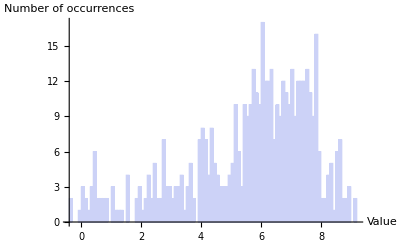

```mathematica
Histogram[data2, 100,AxesLabel->{"Value","Number of occurrences"}]
```

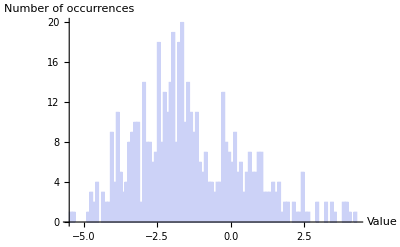

```mathematica
Histogram[data3, 100,AxesLabel->{"Value","Number of occurrences"}]
```

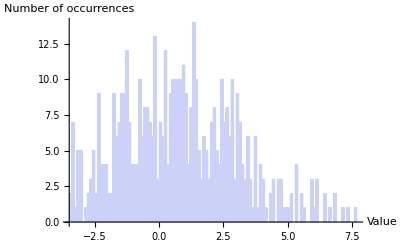

```mathematica
Histogram[data4, 100,AxesLabel->{"Value","Number of occurrences"}]
```

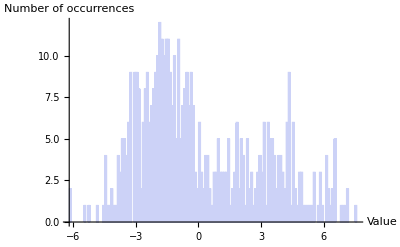

```mathematica
Histogram[data5, 100,AxesLabel->{"Value","Number of occurrences"}]
```

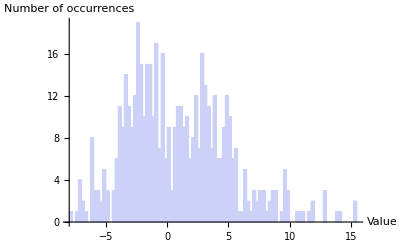

```mathematica
Histogram[data6, 100,AxesLabel->{"Value","Number of occurrences"}]
```

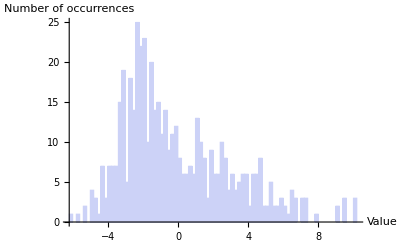

```mathematica
Histogram[data7, 100,AxesLabel->{"Value","Number of occurrences"}]
```

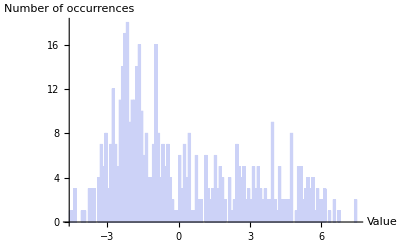

```mathematica
Histogram[data8, 100,AxesLabel->{"Value","Number of occurrences"}]
```

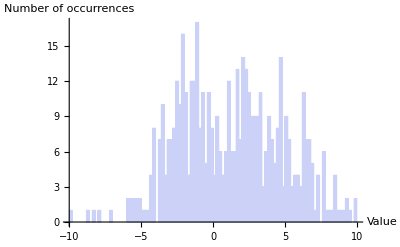

```mathematica
Histogram[data9, 100,AxesLabel->{"Value","Number of occurrences"}]
```

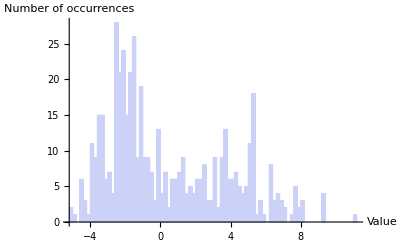

```mathematica
Histogram[data10, 100,AxesLabel->{"Value","Number of occurrences"}]
```

```mathematica
data11 = {-1.3255036400556042,-2.099155902812694,-0.9797174361143104,-0.9797174361143104,-0.9797174361143104,-0.9797174361143104,-0.9797174361143104,-1.2591562505915281,-0.30530899644619136,-1.088346022794989,-1.8461471619849257,-2.5801466347435738,-1.1980251396980839,-1.6886950314738784,-1.6314941709671014,-0.5911047167667178,-1.0096691733734056,-1.0096691733734056,-2.6637975932226685,-2.6637975932226685,-2.6637975932226685,-2.6637975932226685,-3.304317785626764,-2.2602948089841837,-2.0212821906951604,-2.0212821906951604,-2.2712518962383936,-0.16584869039462324,0.39395271505085294,0.7511887758855673,-0.5079910655775564,-0.9056798752382194,-1.1381700322708657,-1.1381700322708657,0.4042156318313612,0.37638731013715293,0.130437788700945,0.38565837340929077,0.945921919086791,-0.7574975590675989,-0.7609138414583442,-0.7609138414583442,-0.7609138414583442,-1.984395794720315,-1.3040184694762624,-0.22540496928603293,-0.3742796382781325,-0.2127688118618748,-0.8664356019179339,0.6027703489384423,1.733563786831545,1.6209200599070013,2.8475804468000443,3.204564638333825,3.204564638333825,1.460335042175096,2.0552720580525583,2.563549600764929,0.6073740481350269,0.9156999781683199,0.716350017024724,-0.00804307737116261,-0.9536694707736031,0.25092315385469366,-0.8792286866746108,-1.892515793639721,-1.726928558452763,-1.5521416418663083,-0.984567622799185,-0.1122210197289315,-0.45521659051606594,-1.7145589802129424,-2.138488020210284,-1.3933686927149913,-1.9682846562448004,-2.7636327221475843,-2.2826763526125506,-3.251669157924205,-3.042360369919645,-1.9331109686944534,-0.4364696116296791,-1.0281160989065379,-1.6095883898228704,-1.6095883898228704,-1.4654446569308137,-1.7382023935954467,-1.7382023935954467,-1.252042236522356,-0.2341466270776047,-1.6428292203382469,0.0439203380368145,0.32669852388392956,0.7271115580042344,1.2513811149598146,0.4461693074721387,-1.5481649074457018,-0.7421167911451632,-2.5528606290854072,-2.5528606290854072,-2.432303491805025,-2.096417944008431,-2.9196199829800134,-2.701851450677458,-1.339610671048363,-2.7680581139801532,-3.133992821240707,-3.491788729254519,-2.0635092529632266,-2.5131368198717743,-0.8023151856026054,-1.1409473635575251,-1.6654407104203082,-1.7972065315775516,-1.7972065315775516,-0.325202297790143,-0.09365827658848583,0.8028304447681984,1.9092119693870906,2.5749387093901177,3.3079013914366664,0.47194948915672397,0.2613127009426796,-0.8119318298497897,-0.3416901174373503,-0.20452730885695874,0.04806124081769492,-0.6055198744334611,0.5256518031303232,-0.7529760892125288,-0.9452103006179289,-0.9452103006179289,-0.8195806347055911,-1.7632599154356048,-1.1976266658626944,-1.3786583270696895,-2.04879585080461,-1.0295194860144012,-1.521908352477443,-3.2405677411756595,-2.199258329525563,-2.024110338580797,-2.1137601070644236,-2.1137601070644236,-2.150294094074384,-1.4198292741264493,-2.3124917918208263,-1.0619223011775982,-1.0619223011775982,-1.0619223011775982,-1.7052681716630198,-1.4398771550844256,-0.793713306869223,-1.9829238238799982,-1.9829238238799982,-1.8857704835765743,-1.8857704835765743,-1.4941082953699112,-3.240398359387493,-2.790722201964108,-3.6418386566900467,-3.6418386566900467,-3.9002303684557615,-3.6233653909308643,-2.920655490877528,-2.770871790809013,-1.6532002791537663,-1.5590755924419333,-0.44020585604118945,0.1520934611669208,1.4772662205946716,0.9752189112646589,2.5485610715750098,3.2265987321826044,3.727426080030229,3.5899500247730067,3.123258439833593,3.646704734256267,3.1836673418403123,3.54213829296268,3.2849780720796167,3.474791330064948,3.0171603175627304,1.5831618117254853,0.842167240612208,1.9237185687635816,1.383394703981446,1.0985153024518215,0.9399134713111618,1.226941000517419,-1.062621085384425,-1.062621085384425,-2.4023294636832593,-3.629831393478065,-3.629831393478065,-3.629831393478065,-3.1557258230683343,-3.1876672341605654,-2.723403842763691,-1.9163004479923305,-1.9163004479923305,-2.54561977811476,-2.8125655025820664,-4.793434366455848,-4.39621514806471,-3.406855648036068,-1.4351886538741558,-1.4351886538741558,-0.6285225152020026,-1.9952464015672926,-3.1707518745244485,-3.1707518745244485,-3.1707518745244485,-1.4500995724567722,-1.4500995724567722,-0.12692281506576042,-2.2825683189714105,-1.46331573724306,-2.5595836505462275,-2.5595836505462275,-3.3715987852106672,-2.814672144113555,-1.8845665448209838,-1.8845665448209838,-2.436875572708083,-2.625572340695371,-2.6810513753063177,-1.8774706878481568,-0.9919700299873914,-1.4693610004147768,-0.8509099563123675,-0.524946170752423,-0.9938093379257179,-3.2901284461943856,-2.7021885978980626,-2.133429782608119,-2.133429782608119,-2.133429782608119,-1.4824681799002568,-1.1662721594040142,-0.8662014757684038,-0.8717305480105225,-0.16866970528354197,0.33273251170580087,1.5099400951819428,0.589084795538094,1.5637913469961207,0.542035966152101,1.6707209128204958,2.8874884034260853,4.154054691159994,5.111658608533406,5.111658608533406,4.5707754815561605,5.092004971421227,4.7487835227145325,4.7487835227145325,4.529849758180668,2.1603070384629155,2.1054869439427475,3.54507132415301,3.6526932903583647,2.2772743693292785,1.4285621642024477,1.7995278428259929,1.2660996921900498,0.2562911595866144,-0.45995097078886393,-0.7638392015650449,-0.7638392015650449,0.7857521578918331,0.849569517424521,1.383179711607248,3.124217927285733,3.355439658494837,3.474957740159304,2.8280529777632295,3.9064500325193148,3.512299054258775,3.103973396686621,2.854517130281019,3.4870022331874724,3.4870022331874724,3.418411640546931,1.4990741411953086,1.5928872386143005,2.8038974186265966,4.2472892585805155,2.3090298790455197,3.2222002659616438,2.693127215237422,2.693127215237422,2.303598232021396,2.541761241616778,1.2216696755523375,-0.36619500034044816,-0.7414615059933762,-0.08331920688691563,1.8048847707578544,1.3265160829492868,0.4174658618348799,1.153100565256913,1.6813181561435075,0.9084503604961564,1.0488845815401506,1.6253380458539017,2.014737564664751,2.1472839204292806,0.27693318682398704,0.19130195819392345,-0.37042423253336176,-1.0984381559946348,-1.5125365738209835,-1.8808424422935892,-2.5343390400957047,-2.878745772799332,-2.8092191837511247,-2.8092191837511247,-3.876543811943596,-2.5225419944788507,-2.1177649081610403,-2.44807234825144,-2.44807234825144,-2.1672907053749393,-0.6269021154336358,-1.1030715911878715,-1.9979208838788576,-1.9979208838788576,-0.3702334747343856,-0.36248815875576945,-0.06454890466094543,-0.6557484859122533,-1.8096025134704965,-1.3427603505520187,-2.3704562807337117,-2.0912838627394383,-1.8706833555119116,-1.857809025660969,-2.843979698626544,-2.0469005325944134,-2.0469005325944134,-2.0469005325944134,-2.0469005325944134,-2.0469005325944134,-1.3541069371578573,-1.8145934717471823,-1.601446445000008,-2.3800835936842795,-2.263054755692193,-0.9288250472606654,-0.9288250472606654,-2.8623051520175053,-2.0649647480071054,-3.3646263840700033,-3.7751044513554524,-4.7889540368236325,-5.463152003668142,-5.703234974875316,-4.646235146387589,-5.241672874024707,-5.241672874024707,-5.241672874024707,-5.847546529074992,-4.986993077125582,-5.325140226022191,-4.359871397340522,-4.179414509822786,-2.5493680367125875,-2.5493680367125875,-2.5493680367125875,-2.5493680367125875,-2.377473704145313,-1.777560399894828,-2.349681701036315,-1.8073568193095415,-1.1519245957023607,-0.4183016416087073,-0.6850973571411006,-1.4582855531945893,-0.06924671393349446,0.7422469054499314,-1.1695374076730884,-2.7240157520161286,-2.4685478606424542,-2.8829138229569367,-2.762007682097466,-2.762007682097466,-2.6133292495130993,-1.9564308943610318,-1.7671515933850983,-3.252889196185395,-3.5797635308631617,-2.045934622663719,-2.4140427740461856,-0.5781257226992471,1.5357100412738913,3.2874104960288943,4.5130815162954505,4.987012594728133,3.9446118373260384,3.2420797251120943,4.610315496134055,4.829317493386486,4.757097708349583,5.36708752754732,5.875669804067111,6.086037637187161,5.935006630425722,6.377891704705671,5.614163140608885,5.491190342210519,3.3643313263618446,4.427903206202701,5.351118654601706,3.4694701903240457,3.1603630800817486,3.688604328345649,5.004428452919563,3.178540746772902,2.712901157956428,3.7537182737538353,3.1484476922105062,3.1484476922105062,0.6811343704770292,-0.24159162828927017,-0.4015717113614091,0.633947063769131,0.7394168250155326,1.6974103522320743,1.0596995838960246,1.7498008215883316,2.160738534210773,1.744162078121634,2.0388134776697937,2.0185986211575235,3.5086914153071778,3.746300436734448,4.002213370187342,6.3676258589402135,6.519054666135057,5.81481920911818,7.076881424040371,5.690289839567639,3.420988959334951,1.2110467383458476,1.6471899829082037,1.7690059383452894,0.8599331992494549,-0.8652032448358812,-0.8652032448358812,0.8967215067619715,0.7190230539478132,0.9611308441464363,3.443403370333204,2.2896375171211267,3.1036027898395866,3.1036027898395866,1.6315175724314945,1.876804013184828,3.530173752675206,2.964784435547627,3.5006608057114237,3.5006608057114237,2.502061443952515,2.615055335325081,3.8584180291577006,4.5045657334255855,4.027419128584988,2.9744636018219257,2.7258985102507753,2.7486482492409454,3.095353352553157,3.2919570587391522,3.3345274071334177,4.266715390384889,4.4215725213046015,3.000474954399419,2.4673655348308303,2.4061614013159898,2.8894888400231524,4.194705511533524,4.597868160278215,5.274187943543342,6.81107348233877,6.607413114684196,7.962776379202475,7.0103048889759725,6.994036286838501,7.865881879332283,6.904089324321383,6.904089324321383,7.201626201595309,7.208503132953512,6.731138574379019,6.731138574379019,6.179976504156714,6.577322455789692,6.161194567110033,6.339755058690414,6.50315484585048,7.174263156922251,6.950297502232333,6.950297502232333,6.076037111795427,6.660584935293653,8.20294007102466,6.774694612995032,6.782900314141927,6.738105231278978,7.050885635170883,7.050885635170883,6.258281466717729,6.529091532104543,7.503290797165647,7.98374798244651,7.98374798244651,8.744644475396356,9.28393932581539,8.487770449614704,8.225252017746024,6.791550596716192,7.3086769380411525,7.576718655415244,6.931148133554,6.699815710382678,6.825065331940407,5.658708180752617,4.464130007817188,4.595598396306114,4.447016900702353,4.96514401569417,4.641609149102543,4.833729491171712,4.833729491171712,3.295831230433465,1.686985059834953,0.856946426546911,0.8513101796583004,1.1330075150396977,0.11708930906905302,-0.9235666420700472,-0.9622262720064891,-1.2135179441167323,-2.6757248784984258,-2.7627305685718513,-1.5516616156635914,-0.5314367920001493,0.26766539269021683,2.8130898248925584,2.8130898248925584,2.5131608329154353,1.728088102451206,3.334169602742289,4.798991248900442,3.67696339222225,3.67696339222225,5.577575539668919,4.498594256500348,4.592807740540774,3.9802667085170014,3.3316370989794537,3.3316370989794537,2.9341654527351424,2.205105076470257,2.2923860700658523,1.7655318790743255,1.3570116536343384,0.061932815728078294,-0.42589263464281746,-1.4777273532219612,-1.3986064213012697,-0.6593605296615377,0.1343945854583689,-0.9160848380387573,-0.9160848380387573,-1.1977578324624685,-0.37461261131166756,-0.4028859553879624,0.7024731857647635,0.9789766946890717,0.9496964982639977,0.14363956572023628,-0.3237274010744095,-0.8184845662978641,0.29469301836242856,1.3199057325633934,-0.0023432853293621214,-0.6789987090139523,-1.1343283003158986,0.29568068754808063,-0.9213531394642183,0.13139796534021575,1.5962279843389666,-0.579708179185574,-0.8252793359947135,-1.9084875902678895,-1.7398974648562076,-0.3000841900085416,-0.3000841900085416,0.31362274424926384,0.054511095311640834,0.9162245958083579,2.535338059990678,1.4077507665427968,-0.43347081160630796,0.26873404911224896,2.3258005064438825,3.9663010699547145,4.237778365521441,2.037200958449529,0.9669952684391732,-2.4737815394929052,-2.7033635983779845,-2.7033635983779845,-2.3050313286891657,-2.3050313286891657,-1.2448182224058046,-1.9140781925797175,-3.544578284973113,-3.544578284973113,-2.9275824223527938,-3.281964371938361,-4.062895866855088,-4.062895866855088,-3.461796164817181,-3.660821998637594,-3.660821998637594,-2.8974432017701597,-3.8001221464797674,-3.8001221464797674,-1.1533075150425063,-2.598269672814912,-2.598269672814912,-2.525928382808543,-2.6268187978381228,-1.7980604766773558,-2.4159398744642333,-2.1817910099792366,-3.3462464367540887,-1.6710410637251345,-1.6710410637251345,-1.6710410637251345,-1.1150031473717767,-1.1150031473717767,-1.1150031473717767,-1.6573268744616647,-1.3524665200941381,-3.7310429634229716,-4.150941092162255,-4.150941092162255,-3.175616307830761,-2.35565500281776,-2.593047810851718,-1.7058880232162357,-1.7058880232162357,-1.0089264462571472,-1.0089264462571472,-3.103212430663227,-3.0336650889806127,-1.4621843710759632,-1.4621843710759632,0.9360139129432701,0.15127584727186594,0.08930495727246973,0.8356339110046893,0.26176337807555217,-1.274464668717274,-2.4934248438582225,-2.307307870137446,-2.1378154043732938,0.06936743158959846,1.5620883002931245,1.0311094824831284,1.9900224972491105,2.0751035832188562,1.0166260152164246,0.7331420508346045,1.4756591042312133,0.18495850574632855,0.6205321494811746,0.3606008068176674,0.7544783908454364,1.7623993534973026,1.7767648285403252,3.7207397391810235,3.6165976580721346,3.3503337800188073,4.1299997360921665,3.135661547190378,1.3222116772314632,1.1922763520323119,0.8712771213937212,1.1374176479747418,2.8762797879809527,0.5448121032645661,-1.0388216308473601,-1.0388216308473601,-0.7945346940783472,-0.1245560271300008,0.6989947937406362,0.8045152429435686,0.29078377377442954,0.49766311428753257,1.1234268092341906,2.27538638975038,1.1814520753209343,2.2812519222224164,0.9530831743777519,2.2344990866861814,-0.05323812483650192,0.2730639949831017,1.8109201593721622,2.5062537165784535,2.18346954407517,1.272936385459373,1.3023140544207503,-0.5467758650616465,-0.5453444086870702,-0.9048594611739655,-2.416645234021109,-2.416645234021109,-0.9632791689403459,-1.2294203164387998,-0.5862430400964133,-1.0408034364987282,-0.9523305724043882,0.9315010360870746,-1.1133420376219139,-0.9596375029584274,-0.9596375029584274,-1.9234663884688525,-3.1193925082483847,-2.1060013623118548,-1.573779455484615,-1.89785667982992,-2.286084011134929,-1.8945335120662437,-1.8945335120662437,-0.9446530440248638,-2.4048990017363328,-1.9081932376210666,-2.146507428881226,-2.0923895151844536,-2.0163380718993165,-1.9878502301333432,-1.9878502301333432,-2.213012314415248,-0.5266908919575222,0.6916568224832531,0.5047898251527752,0.19488111662199553,-2.6040021056113125,-2.2078210837541437,-1.6798382057663988,-2.418237143183466,-2.8165221699430827,-2.5713515084503618,-2.261925070552111,-1.600017778901696,-2.8324302978177602,-2.8324302978177602,-3.571146997673522,-3.2795876858606343,-2.737872485367362,-1.0976157849128083,-0.6702274685145767,-0.7482379022591232,-0.7482379022591232,-3.0935029137318537,-3.0974160389833814,-2.552359270444738,-2.552359270444738,-1.0925034489897785,2.147084724618964,2.1707949647809066,3.1714921492434742,2.2234929633636193,3.86184380226005,4.6434554889025215,3.329469786882756,4.671788447883479,5.559315654556894,4.79842572317207,3.114409895442681,2.2339870282956396,1.1771764590281233,-0.1774254307575791,0.33422837994744126,0.15946599251109808,0.6705818178038859,0.22736158277211005,0.33818693499352775,1.7466949368939635,2.662756099432822,1.4841367341922123,2.172962537081645,0.9340571789370968,1.433746545294723,1.197216675558606,1.5772962807338238,1.1595731275088135,3.3814176801641525,3.426888466642809,4.166375352892104,3.437732597858327,4.723172440666698,2.8079007407263554,2.0140351980801623,2.739592054919356,2.0269107121697765,1.9065131465638132,1.451446283754721,1.365327550115072,1.1314077023803513,2.1361550536179923,1.9720452272328424,2.734268342172434,4.050784636884118,3.7550009562739692,4.643293965687786,5.887171858974628,5.467770790385099,4.987500613697769,4.927717242638527,3.3766137669536755,3.525581995541756,4.053657030167957,5.602404439461583,5.602404439461583,5.54759609692844,6.255718919523519,4.621710507394262,3.572697201741808,2.4160872043671606,2.297631360319575,1.9621757889515903,1.315518779579266,1.5963830554702951,2.3994315720627184,2.3994315720627184,2.019492002385798,1.3227185068780407,0.4449185804527449,0.6191656921158254,1.6002809803022977,1.804399467321753,2.144403830713344,3.555348412412499,3.1030711425597524,4.853048515689597,4.386112669299515,3.769536032247915,3.1253895964242995,3.368259001602957,3.368259001602957,4.588973150592423,5.985511498547083,4.865643632017971,5.119758823169405,3.841451188649205,3.0901612144951844,3.0901612144951844,2.5850413831170918,2.4190294543841286,1.7152293307422046,0.9832522782977707,1.5276308409587873,1.5276308409587873,1.669945264389539,1.0700956095164589,1.4859045940809978,0.8456574971923021,1.1922638729636588,0.5744465363142489,1.8850250695137527,3.203023504218298,2.4338835507683876,3.163976527097307,2.6147783272631786,2.7072100263629695,2.6804450159380875,2.397857708224512,2.04362911443727,3.0935771522565885,1.8838352690606928,1.260095933820357,1.4229799071977325,0.7510149850846868,-0.6232674232409185,-2.0747448925022596,-1.725108406763575,-1.1400672980367879,-1.1400672980367879,-1.6426317570010616,-1.6426317570010616,-2.0996517340363785,-2.3114161681449086,-2.3114161681449086,-2.491690781294382,-2.491690781294382,-1.3759455894998365,-1.6792355281448348,-1.6792355281448348,-1.2836869456147577,-0.9931365607688111,-0.7467811881422532,-0.28940850065972373,-0.6769392874560016,-1.5133995730355037,-0.7548265403726325,-1.2278933322085235,-2.1209552714351907,-2.1209552714351907,-2.4611695817778347,-0.526235332363522,-2.4330586748328313,-1.549375163861996,-0.9055732403271881,-1.0809538939518217,-0.948837218509452,-0.829623069764602,-2.5153956362014482,0.8456390672071596,0.052828335852257435,-1.1110252620780465,-0.7397669726557243,-0.6835132856094848,-2.9046922614584583,-3.5630232795048067,-3.5630232795048067,-1.8402877843263243,-1.8402877843263243,-1.9854826815050193,-1.233393444071296,-2.480088929768609,-2.480088929768609,-2.3230117320389176,-2.9697061022724496,-1.7150542683722303,-2.139666142878276,-2.139666142878276,-2.139666142878276,-1.6330432998932312,-1.7843317622803603,-0.2115262324206446,0.9153620040279629,0.26761767152769544,-0.17802028198770403,-0.9405584898177718,-1.3894330658729832,-1.6581287852834081,-1.2329382671892588,-1.525583130610305,-2.208425621122027,-1.1873074437475473,-1.012287967296271,-2.408542235322508,-2.4014856143876093,-2.4014856143876093,-3.0697860145709477,-1.8838738589064095,-1.8838738589064095,1.281312027639439,1.5401584335746132,0.5661750213560515,-0.26824230416542016,-0.7539067859602436,-0.9932752447481349,0.3390446464119311,1.353690022713157,1.1069125975941856,0.5431897585332899,-0.6712290440366508,-0.17009467246857413,-0.17009467246857413,-0.16302318842171853,-1.2115118402512606,-1.2115118402512606,-0.19986975110041683,-0.7851660529350692,0.7258604335138068,0.3351645904274464,0.5307906843365297,-0.9227528920127454,-0.26413361521856793,-0.2543321294989145,-0.9136169953111372,1.2151211388744403,0.4826727894331755,2.439793864576051,2.8690926248768163,3.0321357494306365,3.9213425141851186,3.891984274771946,3.6323664179901183,5.352325445077186,5.347955979941078,4.571928986798064,4.06554200306689,4.726316805721762,4.726316805721762}
```

{-1.3255,-2.09916,-0.979717,-0.979717,-0.979717,-0.979717,-0.979717,-1.25916,-0.305309,-1.08835,-1.84615,-2.58015,-1.19803,-1.6887,-1.63149,-0.591105,-1.00967,-1.00967,-2.6638,-2.6638,-2.6638,-2.6638,-3.30432,-2.26029,-2.02128,-2.02128,-2.27125,-0.165849,0.393953,0.751189,-0.507991,-0.90568,-1.13817,-1.13817,0.404216,0.376387,0.130438,0.385658,0.945922,-0.757498,-0.760914,-0.760914,-0.760914,-1.9844,-1.30402,-0.225405,-0.37428,-0.212769,-0.866436,0.60277,1.73356,1.62092,2.84758,3.20456,3.20456,1.46034,2.05527,2.56355,0.607374,0.9157,0.71635,-0.00804308,-0.953669,0.250923,-0.879229,-1.89252,-1.72693,-1.55214,-0.984568,-0.112221,-0.455217,-1.71456,-2.13849,-1.39337,-1.96828,-2.76363,-2.28268,-3.25167,-3.04236,-1.93311,-0.43647,-1.02812,-1.60959,-1.60959,-1.46544,-1.7382,-1.7382,-1.25204,-0.234147,-1.64283,0.0439203,0.326699,0.727112,1.25138,0.446169,-1.54816,-0.742117,-2.55286,-2.55286,-2.4323,-2.09642,-2.91962,-2.70185,-1.33961,-2.76806,-3.13399,-3.49179,-2.06351,-2.51314,-0.802315,-1.14095,-1.66544,-1.79721,-1.79721,-0.325202,-0.0936583,0.80283,1.90921,2.57494,3.3079,0.471949,0.261313,-0.811932,-0.34169,-0.204527,0.0480612,-0.60552,0.525652,-0.752976,-0.94521,-0.94521,-0.819581,-1.76326,-1.19763,-1.37866,-2.0488,-1.02952,-1.52191,-3.24057,-2.19926,-2.02411,-2.11376,-2.11376,-2.15029,-1.41983,-2.31249,-1.06192,-1.06192,-1.06192,-1.70527,-1.43988,-0.793713,-1.98292,-1.98292,-1.88577,-1.88577,-1.49411,-3.2404,-2.79072,-3.64184,-3.64184,-3.90023,-3.62337,-2.92066,-2.77087,-1.6532,-1.55908,-0.440206,0.152093,1.47727,0.975219,2.54856,3.2266,3.72743,3.58995,3.12326,3.6467,3.18367,3.54214,3.28498,3.47479,3.01716,1.58316,0.842167,1.92372,1.38339,1.09852,0.939913,1.22694,-1.06262,-1.06262,-2.40233,-3.62983,-3.62983,-3.62983,-3.15573,-3.18767,-2.7234,-1.9163,-1.9163,-2.54562,-2.81257,-4.79343,-4.39622,-3.40686,-1.43519,-1.43519,-0.628523,-1.99525,-3.17075,-3.17075,-3.17075,-1.4501,-1.4501,-0.126923,-2.28257,-1.46332,-2.55958,-2.55958,-3.3716,-2.81467,-1.88457,-1.88457,-2.43688,-2.62557,-2.68105,-1.87747,-0.99197,-1.46936,-0.85091,-0.524946,-0.993809,-3.29013,-2.70219,-2.13343,-2.13343,-2.13343,-1.48247,-1.16627,-0.866201,-0.871731,-0.16867,0.332733,1.50994,0.589085,1.56379,0.542036,1.67072,2.88749,4.15405,5.11166,5.11166,4.57078,5.092,4.74878,4.74878,4.52985,2.16031,2.10549,3.54507,3.65269,2.27727,1.42856,1.79953,1.2661,0.256291,-0.459951,-0.763839,-0.763839,0.785752,0.84957,1.38318,3.12422,3.35544,3.47496,2.82805,3.90645,3.5123,3.10397,2.85452,3.487,3.487,3.41841,1.49907,1.59289,2.8039,4.24729,2.30903,3.2222,2.69313,2.69313,2.3036,2.54176,1.22167,-0.366195,-0.741462,-0.0833192,1.80488,1.32652,0.417466,1.1531,1.68132,0.90845,1.04888,1.62534,2.01474,2.14728,0.276933,0.191302,-0.370424,-1.09844,-1.51254,-1.88084,-2.53434,-2.87875,-2.80922,-2.80922,-3.87654,-2.52254,-2.11776,-2.44807,-2.44807,-2.16729,-0.626902,-1.10307,-1.99792,-1.99792,-0.370233,-0.362488,-0.0645489,-0.655748,-1.8096,-1.34276,-2.37046,-2.09128,-1.87068,-1.85781,-2.84398,-2.0469,-2.0469,-2.0469,-2.0469,-2.0469,-1.35411,-1.81459,-1.60145,-2.38008,-2.26305,-0.928825,-0.928825,-2.86231,-2.06496,-3.36463,-3.7751,-4.78895,-5.46315,-5.70323,-4.64624,-5.24167,-5.24167,-5.24167,-5.84755,-4.98699,-5.32514,-4.35987,-4.17941,-2.54937,-2.54937,-2.54937,-2.54937,-2.37747,-1.77756,-2.34968,-1.80736,-1.15192,-0.418302,-0.685097,-1.45829,-0.0692467,0.742247,-1.16954,-2.72402,-2.46855,-2.88291,-2.76201,-2.76201,-2.61333,-1.95643,-1.76715,-3.25289,-3.57976,-2.04593,-2.41404,-0.578126,1.53571,3.28741,4.51308,4.98701,3.94461,3.24208,4.61032,4.82932,4.7571,5.36709,5.87567,6.08604,5.93501,6.37789,5.61416,5.49119,3.36433,4.4279,5.35112,3.46947,3.16036,3.6886,5.00443,3.17854,2.7129,3.75372,3.14845,3.14845,0.681134,-0.241592,-0.401572,0.633947,0.739417,1.69741,1.0597,1.7498,2.16074,1.74416,2.03881,2.0186,3.50869,3.7463,4.00221,6.36763,6.51905,5.81482,7.07688,5.69029,3.42099,1.21105,1.64719,1.76901,0.859933,-0.865203,-0.865203,0.896722,0.719023,0.961131,3.4434,2.28964,3.1036,3.1036,1.63152,1.8768,3.53017,2.96478,3.50066,3.50066,2.50206,2.61506,3.85842,4.50457,4.02742,2.97446,2.7259,2.74865,3.09535,3.29196,3.33453,4.26672,4.42157,3.00047,2.46737,2.40616,2.88949,4.19471,4.59787,5.27419,6.81107,6.60741,7.96278,7.0103,6.99404,7.86588,6.90409,6.90409,7.20163,7.2085,6.73114,6.73114,6.17998,6.57732,6.16119,6.33976,6.50315,7.17426,6.9503,6.9503,6.07604,6.66058,8.20294,6.77469,6.7829,6.73811,7.05089,7.05089,6.25828,6.52909,7.50329,7.98375,7.98375,8.74464,9.28394,8.48777,8.22525,6.79155,7.30868,7.57672,6.93115,6.69982,6.82507,5.65871,4.46413,4.5956,4.44702,4.96514,4.64161,4.83373,4.83373,3.29583,1.68699,0.856946,0.85131,1.13301,0.117089,-0.923567,-0.962226,-1.21352,-2.67572,-2.76273,-1.55166,-0.531437,0.267665,2.81309,2.81309,2.51316,1.72809,3.33417,4.79899,3.67696,3.67696,5.57758,4.49859,4.59281,3.98027,3.33164,3.33164,2.93417,2.20511,2.29239,1.76553,1.35701,0.0619328,-0.425893,-1.47773,-1.39861,-0.659361,0.134395,-0.916085,-0.916085,-1.19776,-0.374613,-0.402886,0.702473,0.978977,0.949696,0.14364,-0.323727,-0.818485,0.294693,1.31991,-0.00234329,-0.678999,-1.13433,0.295681,-0.921353,0.131398,1.59623,-0.579708,-0.825279,-1.90849,-1.7399,-0.300084,-0.300084,0.313623,0.0545111,0.916225,2.53534,1.40775,-0.433471,0.268734,2.3258,3.9663,4.23778,2.0372,0.966995,-2.47378,-2.70336,-2.70336,-2.30503,-2.30503,-1.24482,-1.91408,-3.54458,-3.54458,-2.92758,-3.28196,-4.0629,-4.0629,-3.4618,-3.66082,-3.66082,-2.89744,-3.80012,-3.80012,-1.15331,-2.59827,-2.59827,-2.52593,-2.62682,-1.79806,-2.41594,-2.18179,-3.34625,-1.67104,-1.67104,-1.67104,-1.115,-1.115,-1.115,-1.65733,-1.35247,-3.73104,-4.15094,-4.15094,-3.17562,-2.35566,-2.59305,-1.70589,-1.70589,-1.00893,-1.00893,-3.10321,-3.03367,-1.46218,-1.46218,0.936014,0.151276,0.089305,0.835634,0.261763,-1.27446,-2.49342,-2.30731,-2.13782,0.0693674,1.56209,1.03111,1.99002,2.0751,1.01663,0.733142,1.47566,0.184959,0.620532,0.360601,0.754478,1.7624,1.77676,3.72074,3.6166,3.35033,4.13,3.13566,1.32221,1.19228,0.871277,1.13742,2.87628,0.544812,-1.03882,-1.03882,-0.794535,-0.124556,0.698995,0.804515,0.290784,0.497663,1.12343,2.27539,1.18145,2.28125,0.953083,2.2345,-0.0532381,0.273064,1.81092,2.50625,2.18347,1.27294,1.30231,-0.546776,-0.545344,-0.904859,-2.41665,-2.41665,-0.963279,-1.22942,-0.586243,-1.0408,-0.952331,0.931501,-1.11334,-0.959638,-0.959638,-1.92347,-3.11939,-2.106,-1.57378,-1.89786,-2.28608,-1.89453,-1.89453,-0.944653,-2.4049,-1.90819,-2.14651,-2.09239,-2.01634,-1.98785,-1.98785,-2.21301,-0.526691,0.691657,0.50479,0.194881,-2.604,-2.20782,-1.67984,-2.41824,-2.81652,-2.57135,-2.26193,-1.60002,-2.83243,-2.83243,-3.57115,-3.27959,-2.73787,-1.09762,-0.670227,-0.748238,-0.748238,-3.0935,-3.09742,-2.55236,-2.55236,-1.0925,2.14708,2.17079,3.17149,2.22349,3.86184,4.64346,3.32947,4.67179,5.55932,4.79843,3.11441,2.23399,1.17718,-0.177425,0.334228,0.159466,0.670582,0.227362,0.338187,1.74669,2.66276,1.48414,2.17296,0.934057,1.43375,1.19722,1.5773,1.15957,3.38142,3.42689,4.16638,3.43773,4.72317,2.8079,2.01404,2.73959,2.02691,1.90651,1.45145,1.36533,1.13141,2.13616,1.97205,2.73427,4.05078,3.755,4.64329,5.88717,5.46777,4.9875,4.92772,3.37661,3.52558,4.05366,5.6024,5.6024,5.5476,6.25572,4.62171,3.5727,2.41609,2.29763,1.96218,1.31552,1.59638,2.39943,2.39943,2.01949,1.32272,0.444919,0.619166,1.60028,1.8044,2.1444,3.55535,3.10307,4.85305,4.38611,3.76954,3.12539,3.36826,3.36826,4.58897,5.98551,4.86564,5.11976,3.84145,3.09016,3.09016,2.58504,2.41903,1.71523,0.983252,1.52763,1.52763,1.66995,1.0701,1.4859,0.845657,1.19226,0.574447,1.88503,3.20302,2.43388,3.16398,2.61478,2.70721,2.68045,2.39786,2.04363,3.09358,1.88384,1.2601,1.42298,0.751015,-0.623267,-2.07474,-1.72511,-1.14007,-1.14007,-1.64263,-1.64263,-2.09965,-2.31142,-2.31142,-2.49169,-2.49169,-1.37595,-1.67924,-1.67924,-1.28369,-0.993137,-0.746781,-0.289409,-0.676939,-1.5134,-0.754827,-1.22789,-2.12096,-2.12096,-2.46117,-0.526235,-2.43306,-1.54938,-0.905573,-1.08095,-0.948837,-0.829623,-2.5154,0.845639,0.0528283,-1.11103,-0.739767,-0.683513,-2.90469,-3.56302,-3.56302,-1.84029,-1.84029,-1.98548,-1.23339,-2.48009,-2.48009,-2.32301,-2.96971,-1.71505,-2.13967,-2.13967,-2.13967,-1.63304,-1.78433,-0.211526,0.915362,0.267618,-0.17802,-0.940558,-1.38943,-1.65813,-1.23294,-1.52558,-2.20843,-1.18731,-1.01229,-2.40854,-2.40149,-2.40149,-3.06979,-1.88387,-1.88387,1.28131,1.54016,0.566175,-0.268242,-0.753907,-0.993275,0.339045,1.35369,1.10691,0.54319,-0.671229,-0.170095,-0.170095,-0.163023,-1.21151,-1.21151,-0.19987,-0.785166,0.72586,0.335165,0.530791,-0.922753,-0.264134,-0.254332,-0.913617,1.21512,0.482673,2.43979,2.86909,3.03214,3.92134,3.89198,3.63237,5.35233,5.34796,4.57193,4.06554,4.72632,4.72632}

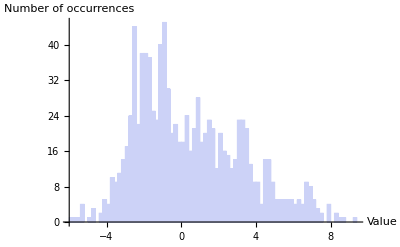

```mathematica
Histogram[data11, 100,AxesLabel->{"Value","Number of occurrences"}]
```